# Hybrid fitness in Haploids

```mathematica
(*Parameter settings & Read file*)
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop2_0.dat"];
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*fixation during adaptive phase*)
Length@TakeWhile[Sign[slistpop1],#>0.5&];
Length@TakeWhile[Sign[slistpop2],#>0.5&];
(*fixation during adaptive phase & circling optimum*)
2*Length@TakeWhile[Sign[slistpop1],#>0.5&];
2*Length@TakeWhile[Sign[slistpop2],#>0.5&];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
Length@slistpop1
Length@slistpop2
```

184

176

```mathematica
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
```

## Fitness within the population

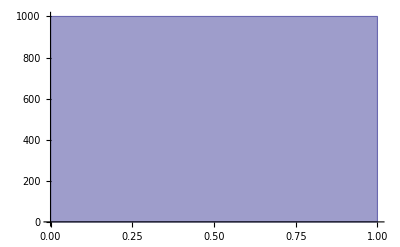

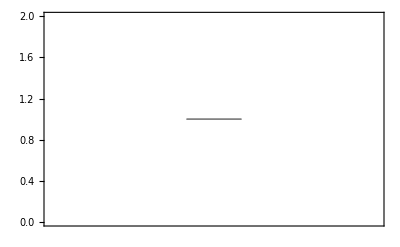

```mathematica
Pop1fitness={};
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]

Histogram[{Pop1fitness}]
BoxWhiskerChart[{Pop1fitness}]
```

## F1 fitness

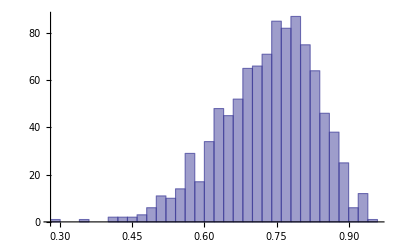

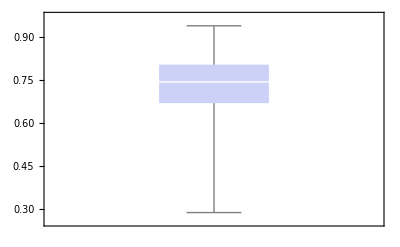

```mathematica
F1fitness={};
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];
Histogram[{F1fitness}]
BoxWhiskerChart[{F1fitness}]
```

## F2 fitness

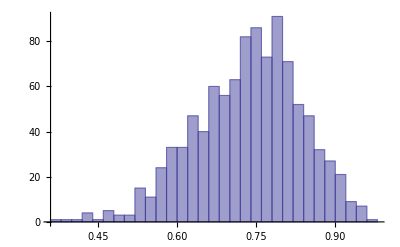

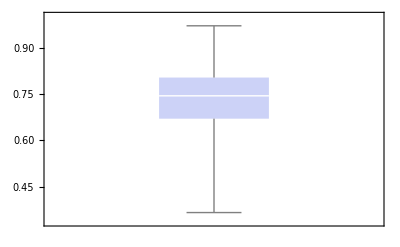

```mathematica
F2fitness={};
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]

Histogram[{F2fitness}]
BoxWhiskerChart[{F2fitness}]
```

## Backcross fitness (pop1 * F1)

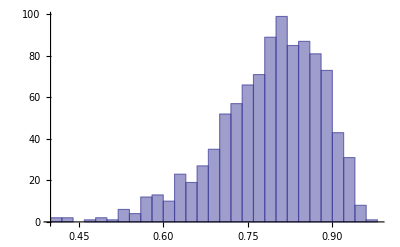

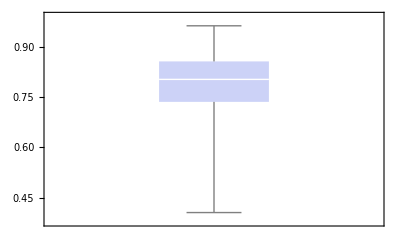

```mathematica
BC1fitness={};
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]

Histogram[{BC1fitness}]
BoxWhiskerChart[{BC1fitness}]
```

{0.998847,0.732764,0.735333,0.788355}

{1.49955×10^-14,0.0990364,0.100189,0.0921965}

{0.998847→1.49955×10^-14,0.732764→0.0990364,0.735333→0.100189,0.788355→0.0921965}

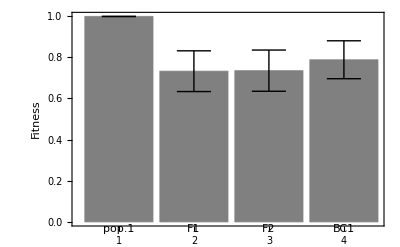

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

# Hybrid fitness in diploids

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)

pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r=0.04_pop2_0.dat"];
```

```mathematica
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*fixation during adaptive phase*)
Length@TakeWhile[Sign[slistpop1],#>0.5&];
Length@TakeWhile[Sign[slistpop2],#>0.5&];
(*fixation during adaptive phase & circling optimum*)
2*Length@TakeWhile[Sign[slistpop1],#>0.5&];
2*Length@TakeWhile[Sign[slistpop2],#>0.5&];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
Length@slistpop1
Length@slistpop2
```

184

204

```mathematica
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
```

## Fitness within the population

```mathematica
Pop1fitness={};
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]

Histogram[{Pop1fitness}]
BoxWhiskerChart[{Pop1fitness}]
```

-Graphics-

-Graphics-

## F1 fitness

-Graphics-

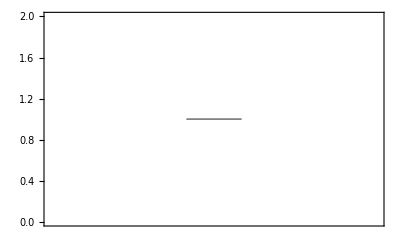

```mathematica
F1fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];
Histogram[{F1fitness}]
BoxWhiskerChart[{F1fitness}]
```

## F2 fitness

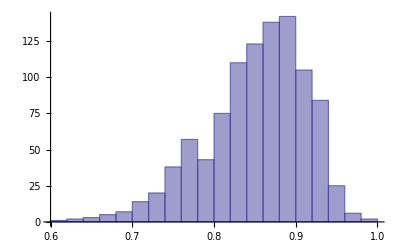

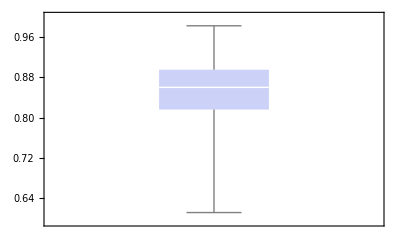

```mathematica
F2fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]
Histogram[{F2fitness}]
BoxWhiskerChart[{F2fitness}]
```

## Backcross fitness (pop1 * F1)

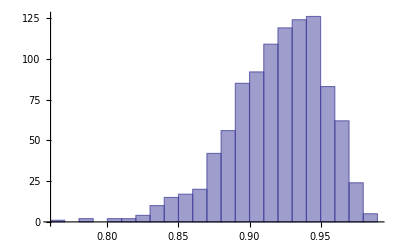

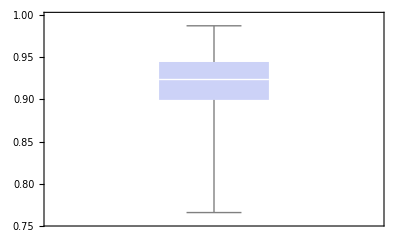

```mathematica
BC1fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]
Histogram[{BC1fitness}]
BoxWhiskerChart[{BC1fitness}]
```

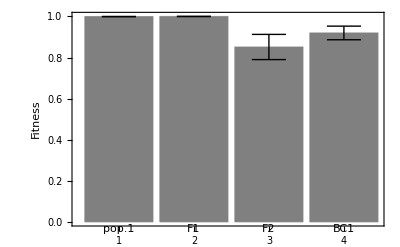

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

## Figure 2

### (a) Haploid(λ=0.04)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];

(*F2*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*BC1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

];
```

{0.998847,0.731681,0.737916,0.788242}

{1.49955×10^-14,0.101146,0.100326,0.0905563}

{0.998847→1.49955×10^-14,0.731681→0.101146,0.737916→0.100326,0.788242→0.0905563}

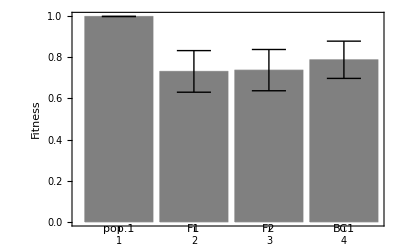

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

```mathematica
Export["~/Desktop/Figure3_Haploid_a.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

### (b) Diploid(λ=0.04)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
 ;];

(*BC1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

];
```

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

{0.999273,0.999784,0.852461,0.921533}

{2.01051×10^-14,2.67698×10^-14,0.0632371,0.0318199}

{0.999273→2.01051×10^-14,0.999784→2.67698×10^-14,0.852461→0.0632371,0.921533→0.0318199}

```mathematica
Export["~/Desktop/Figure3_Diploid_b.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

### (c) Haploid(λ=0.12)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.12]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.12]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];

(*F2*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*BC1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

];
```

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

```mathematica
Export["~/Desktop/Figure3_Haploid_c.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

### (d) Diploid(λ=0.12)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.12]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.12]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
 ;];

(*BC1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

];
```

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

{0.999273,0.999784,0.852461,0.921533}

{2.01051×10^-14,2.67698×10^-14,0.0632371,0.0318199}

{0.999273→2.01051×10^-14,0.999784→2.67698×10^-14,0.852461→0.0632371,0.921533→0.0318199}

```mathematica
Export["~/Desktop/Figure3_Diploid_d.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

## Figure 2 (primary vs. pleiotropic effects)

### (a) Haploid(λ=0.04)

## primary effect

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];(*Calculating fitness of F1*)
];

(*F2*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];
];

(*BC1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];
];

];
```

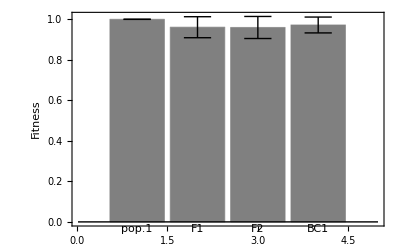

{0.998847→0.,0.96001→0.0517943,0.958677→0.054382,0.971013→0.0390939}

{0.,0.0517943,0.054382,0.0390939}

{0.998847,0.96001,0.958677,0.971013}

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

```mathematica
Export["~/Desktop/Figure2_Haploid_a_primary.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

```mathematica
"~/Desktop/Figure2_Haploid_a_primary.csv"
```

```mathematica
cur
opt
```

{1.8201,-0.228587,0.22271,-0.166626,0.0822486,0.329566,-0.0855344,0.0825585,-0.166828,-0.154279}

{2,0,0,0,0,0,0,0,0,0}

```mathematica
EuclideanDistance[cur,opt]
```

0.585768

```mathematica
EuclideanDistance[cur[[1]],opt[[1]]]
EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]]
```

0.179899

0.557459

## pleiotropic effect

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];(*Calculating fitness of F1*)
];

(*F2*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];
];

(*BC1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];
];

];
```

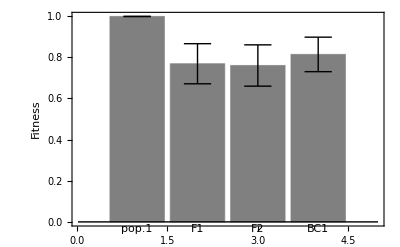

{0.998847→0.,0.768959→0.0974992,0.760378→0.100443,0.814306→0.0838824}

{0.,0.0974992,0.100443,0.0838824}

{0.998847,0.768959,0.760378,0.814306}

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

```mathematica
Export["~/Desktop/Figure2_Haploid_a_pleiotropic.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

```mathematica
"~/Desktop/Figure2_Haploid_a_pleiotropic.csv"
```

## all effects

{0.998847,0.731681,0.737916,0.788242}

{1.49955×10^-14,0.101146,0.100326,0.0905563}

{0.998847→1.49955×10^-14,0.731681→0.101146,0.737916→0.100326,0.788242→0.0905563}

-Graphics-

```mathematica
primary=Import["~/Desktop/Figure2_Haploid_a_primary.csv"];
pleiotropic=Import["~/Desktop/Figure2_Haploid_a_pleiotropic.csv"];
primaryPop1=Transpose[Drop[primary,1][[1;;1000;;1]]][[1]];
primaryF1=Transpose[Drop[primary,1][[1001;;2000;;1]]][[1]];
primaryF2=Transpose[Drop[primary,1][[2001;;3000;;1]]][[1]];
primaryBC1=Transpose[Drop[primary,1][[3001;;4000;;1]]][[1]];
pleiotropicPop1=Transpose[Drop[pleiotropic,1][[1;;1000;;1]]][[1]];
pleiotropicF1=Transpose[Drop[pleiotropic,1][[1001;;2000;;1]]][[1]];
pleiotropicF2=Transpose[Drop[pleiotropic,1][[2001;;3000;;1]]][[1]];
pleiotropicBC1=Transpose[Drop[pleiotropic,1][[3001;;4000;;1]]][[1]];
```

```mathematica
Mean[primaryPop1-primaryF1]
Mean[pleiotropicPop1-pleiotropicF1]
```

0.0388367

0.229888

```mathematica
PieChart[{Mean[pleiotropicPop1-pleiotropicF1],Mean[primaryPop1-primaryF1]},SectorOrigin->Pi/2,PlotLabel->"F1"]
PieChart[{Mean[pleiotropicPop1-pleiotropicF2],Mean[primaryPop1-primaryF2]},SectorOrigin->Pi/2,PlotLabel->"F2"]
PieChart[{Mean[pleiotropicPop1-pleiotropicBC1],Mean[primaryPop1-primaryBC1]},SectorOrigin->Pi/2,PlotLabel->"BC1"]
```

-Graphics-

-Graphics-

-Graphics-

### (b) Diploid(λ=0.04)

## primary effect

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];(*Calculating fitness of F1*)
];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];
 ;];

(*BC1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];
];

];
```

{0.999273,0.999985,0.976518,0.988138}

{0.,0.,0.0321586,0.0161934}

{0.999273→0.,0.999985→0.,0.976518→0.0321586,0.988138→0.0161934}

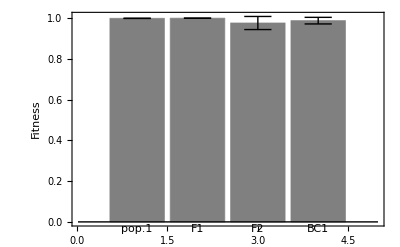

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

```mathematica
Export["~/Desktop/Figure2_Diploid_b_primary.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

```mathematica
"~/Desktop/Figure2_Diploid_b_primary.csv"
```

## pleiotropic effect

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];(*Calculating fitness of F1*)
];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];
 ;];

(*BC1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];
];

];
```

{0.999273,0.999799,0.871045,0.931106}

{0.,0.,0.0562781,0.0302498}

{0.999273→0.,0.999799→0.,0.871045→0.0562781,0.931106→0.0302498}

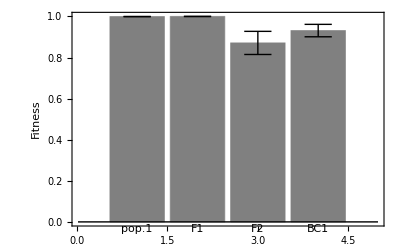

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

```mathematica
Export["~/Desktop/Figure2_Diploid_b_pleiotropic.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

```mathematica
"~/Desktop/Figure2_Diploid_b_pleiotropic.csv"
```

## all effects

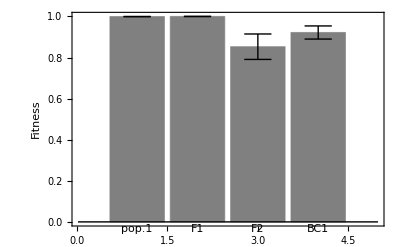

{0.999273→0.,0.999784→0.,0.85259→0.061917,0.921714→0.0319521}

{0.,0.,0.061917,0.0319521}

{0.999273,0.999784,0.85259,0.921714}

{0.999273,0.999784,0.852461,0.921533}

{2.01051×10^-14,2.67698×10^-14,0.0632371,0.0318199}

{0.999273→2.01051×10^-14,0.999784→2.67698×10^-14,0.852461→0.0632371,0.921533→0.0318199}

```mathematica
primary=Import["~/Desktop/Figure2_Diploid_b_primary.csv"];
pleiotropic=Import["~/Desktop/Figure2_Diploid_b_pleiotropic.csv"];
primaryPop1=Transpose[Drop[primary,1][[1;;1000;;1]]][[1]];
primaryF1=Transpose[Drop[primary,1][[1001;;2000;;1]]][[1]];
primaryF2=Transpose[Drop[primary,1][[2001;;3000;;1]]][[1]];
primaryBC1=Transpose[Drop[primary,1][[3001;;4000;;1]]][[1]];
pleiotropicPop1=Transpose[Drop[pleiotropic,1][[1;;1000;;1]]][[1]];
pleiotropicF1=Transpose[Drop[pleiotropic,1][[1001;;2000;;1]]][[1]];
pleiotropicF2=Transpose[Drop[pleiotropic,1][[2001;;3000;;1]]][[1]];
pleiotropicBC1=Transpose[Drop[pleiotropic,1][[3001;;4000;;1]]][[1]];
```

```mathematica
PieChart[{Mean[pleiotropicPop1-pleiotropicF1],Mean[primaryPop1-primaryF1]},SectorOrigin->Pi/2,PlotLabel->"F1"]
PieChart[{Mean[pleiotropicPop1-pleiotropicF2],Mean[primaryPop1-primaryF2]},SectorOrigin->Pi/2,PlotLabel->"F2"]
PieChart[{Mean[pleiotropicPop1-pleiotropicBC1],Mean[primaryPop1-primaryBC1]},SectorOrigin->Pi/2,PlotLabel->"BC1"]
```

-Graphics-

-Graphics-

-Graphics-

### (c) Haploid(λ=0.12)

## primary effect

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.12]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.12]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];(*Calculating fitness of F1*)
];

(*F2*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];
];

(*BC1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];
];

];
```

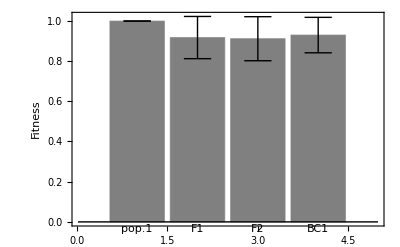

{0.998072→0.,0.916173→0.104903,0.910464→0.109473,0.928523→0.0881027}

{0.,0.104903,0.109473,0.0881027}

{0.998072,0.916173,0.910464,0.928523}

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

```mathematica
Export["~/Desktop/Figure2_Haploid_c_primary.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

```mathematica
"~/Desktop/Figure2_Haploid_c_primary.csv"
```

## pleiotropic effect

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.12]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.12]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];(*Calculating fitness of F1*)
];

(*F2*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];
];

(*BC1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];
];

];
```

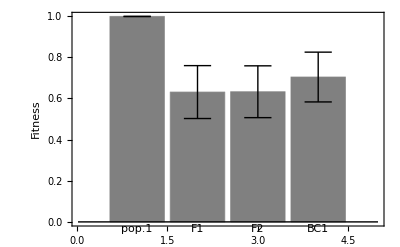

{0.998072→0.,0.630715→0.128497,0.632342→0.12588,0.703769→0.120934}

{0.,0.128497,0.12588,0.120934}

{0.998072,0.630715,0.632342,0.703769}

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

```mathematica
Export["~/Desktop/Figure2_Haploid_c_pleiotropic.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

```mathematica
"~/Desktop/Figure2_Haploid_c_pleiotropic.csv"
```

## all effects

{0.998072,0.56965,0.575166,0.658846}

{0.,0.134054,0.138219,0.129962}

{0.998072→0.,0.56965→0.134054,0.575166→0.138219,0.658846→0.129962}

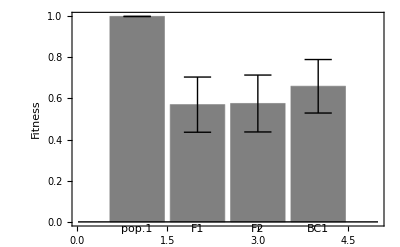

```mathematica
Export["~/Desktop/Figure3_Haploid_c.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

```mathematica
primary=Import["~/Desktop/Figure2_Haploid_c_primary.csv"];
pleiotropic=Import["~/Desktop/Figure2_Haploid_c_pleiotropic.csv"];
primaryPop1=Transpose[Drop[primary,1][[1;;1000;;1]]][[1]];
primaryF1=Transpose[Drop[primary,1][[1001;;2000;;1]]][[1]];
primaryF2=Transpose[Drop[primary,1][[2001;;3000;;1]]][[1]];
primaryBC1=Transpose[Drop[primary,1][[3001;;4000;;1]]][[1]];
pleiotropicPop1=Transpose[Drop[pleiotropic,1][[1;;1000;;1]]][[1]];
pleiotropicF1=Transpose[Drop[pleiotropic,1][[1001;;2000;;1]]][[1]];
pleiotropicF2=Transpose[Drop[pleiotropic,1][[2001;;3000;;1]]][[1]];
pleiotropicBC1=Transpose[Drop[pleiotropic,1][[3001;;4000;;1]]][[1]];
```

```mathematica
PieChart[{Mean[pleiotropicPop1-pleiotropicF1],Mean[primaryPop1-primaryF1]},SectorOrigin->Pi/2,PlotLabel->"F1"]
PieChart[{Mean[pleiotropicPop1-pleiotropicF2],Mean[primaryPop1-primaryF2]},SectorOrigin->Pi/2,PlotLabel->"F2"]
PieChart[{Mean[pleiotropicPop1-pleiotropicBC1],Mean[primaryPop1-primaryBC1]},SectorOrigin->Pi/2,PlotLabel->"BC1"]
```

-Graphics-

-Graphics-

-Graphics-

### (d) Diploid(λ=0.12)

## primary effect

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.12]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.12]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];(*Calculating fitness of F1*)
];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];
 ;];

(*BC1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur[[1]],opt[[1]]])^k]];
];

];
```

{0.997224,0.999965,0.955265,0.975961}

{0.,0.,0.058678,0.03132}

{0.997224→0.,0.999965→0.,0.955265→0.058678,0.975961→0.03132}

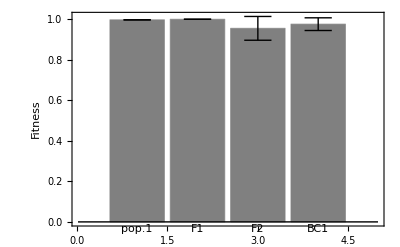

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

```mathematica
Export["~/Desktop/Figure2_Diploid_d_primary.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

```mathematica
"~/Desktop/Figure2_Diploid_d_primary.csv"
```

## pleiotropic effect

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.12]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.12]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];(*Calculating fitness of F1*)
];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];
 ;];

(*BC1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur[[2;;10;;1]],opt[[2;;10;;1]]])^k]];
];

];
```

{0.997224,0.999186,0.73112,0.852556}

{0.,0.,0.11106,0.0634262}

{0.997224→0.,0.999186→0.,0.73112→0.11106,0.852556→0.0634262}

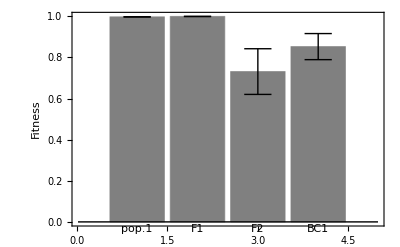

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

```mathematica
Export["~/Desktop/Figure2_Diploid_d_pleiotropic.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

```mathematica
"~/Desktop/Figure2_Diploid_d_pleiotropic.csv"
```

## all effects

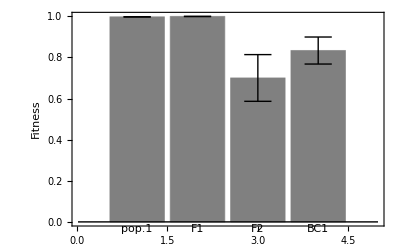

{0.997224→0.,0.999152→0.,0.700038→0.113583,0.833434→0.0657215}

{0.,0.,0.113583,0.0657215}

{0.997224,0.999152,0.700038,0.833434}

```mathematica
Export["~/Desktop/Figure2_Diploid_d.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

```mathematica
primary=Import["~/Desktop/Figure2_Diploid_d_primary.csv"];
pleiotropic=Import["~/Desktop/Figure2_Diploid_d_pleiotropic.csv"];
primaryPop1=Transpose[Drop[primary,1][[1;;1000;;1]]][[1]];
primaryF1=Transpose[Drop[primary,1][[1001;;2000;;1]]][[1]];
primaryF2=Transpose[Drop[primary,1][[2001;;3000;;1]]][[1]];
primaryBC1=Transpose[Drop[primary,1][[3001;;4000;;1]]][[1]];
pleiotropicPop1=Transpose[Drop[pleiotropic,1][[1;;1000;;1]]][[1]];
pleiotropicF1=Transpose[Drop[pleiotropic,1][[1001;;2000;;1]]][[1]];
pleiotropicF2=Transpose[Drop[pleiotropic,1][[2001;;3000;;1]]][[1]];
pleiotropicBC1=Transpose[Drop[pleiotropic,1][[3001;;4000;;1]]][[1]];
```

```mathematica
PieChart[{Mean[pleiotropicPop1-pleiotropicF1],Mean[primaryPop1-primaryF1]},SectorOrigin->Pi/2,PlotLabel->"F1"]
PieChart[{Mean[pleiotropicPop1-pleiotropicF2],Mean[primaryPop1-primaryF2]},SectorOrigin->Pi/2,PlotLabel->"F2"]
PieChart[{Mean[pleiotropicPop1-pleiotropicBC1],Mean[primaryPop1-primaryBC1]},SectorOrigin->Pi/2,PlotLabel->"BC1"]
```

-Graphics-

-Graphics-

-Graphics-

## Figure 3

### (a) Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
mutsize={0.04,0.08,0.12} ;

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤3,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,N[Exp[-q(EuclideanDistance[cur,opt])^k],{Infinity,5}]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];


(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,N[Exp[-q(EuclideanDistance[cur,opt])^k],{Infinity,5}]];(*Calculating fitness of F1*)
];

AppendTo[F1fitnessMean,Mean@F1fitness]

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure3_Haploid_a1.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]]],Join[Table["Pop1small",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1medium",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1large",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["F1small",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1medium",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1large",{i,1,Length@F1fitnesslist[[3]],1}]]},{"Fitness","Hybrid Type"}]];
```

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0}};
scenario={1.1,3.1,3.2,3.3};
mutsize={0.04,0.08,0.12} ;

Pop1fitnesslist={};
F1fitnesslist={};

For[L=1,L≤4,L++,

For[J=1,J≤3,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]];(*Calculating fitness of F1*)
];
AppendTo[F1fitnessMean,Mean@F1fitness];

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];

];
```

```mathematica
Export["~/Desktop/Figure3_Haploid_a2.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],Pop1fitnesslist[[5]],Pop1fitnesslist[[6]],Pop1fitnesslist[[7]],Pop1fitnesslist[[8]],Pop1fitnesslist[[9]],Pop1fitnesslist[[10]],Pop1fitnesslist[[11]],Pop1fitnesslist[[12]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]],F1fitnesslist[[4]],F1fitnesslist[[5]],F1fitnesslist[[6]],F1fitnesslist[[7]],F1fitnesslist[[8]],F1fitnesslist[[9]],F1fitnesslist[[10]],F1fitnesslist[[11]],F1fitnesslist[[12]]],Join[Table["Pop1small_0",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1medium_0",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1large_0",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1small_30",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["Pop1medium_30",{i,1,Length@Pop1fitnesslist[[5]],1}],Table["Pop1large_30",{i,1,Length@Pop1fitnesslist[[6]],1}],Table["Pop1small_45",{i,1,Length@Pop1fitnesslist[[7]],1}],Table["Pop1medium_45",{i,1,Length@Pop1fitnesslist[[8]],1}],Table["Pop1large_45",{i,1,Length@Pop1fitnesslist[[9]],1}],Table["Pop1small_90",{i,1,Length@Pop1fitnesslist[[10]],1}],Table["Pop1medium_90",{i,1,Length@Pop1fitnesslist[[11]],1}],Table["Pop1large_90",{i,1,Length@Pop1fitnesslist[[12]],1}],Table["F1small_0",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1medium_0",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1large_0",{i,1,Length@F1fitnesslist[[3]],1}],Table["F1small_30",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["F1medium_30",{i,1,Length@Pop1fitnesslist[[5]],1}],Table["F1large_30",{i,1,Length@Pop1fitnesslist[[6]],1}],Table["F1small_45",{i,1,Length@Pop1fitnesslist[[7]],1}],Table["F1medium_45",{i,1,Length@Pop1fitnesslist[[8]],1}],Table["F1large_45",{i,1,Length@Pop1fitnesslist[[9]],1}],Table["F1small_90",{i,1,Length@Pop1fitnesslist[[10]],1}],Table["F1medium_90",{i,1,Length@Pop1fitnesslist[[11]],1}],Table["F1large_90",{i,1,Length@Pop1fitnesslist[[12]],1}]]},{"Fitness","Hybrid Type"}]];
```

### (b) Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0}};
scenario={1.1,3.1,3.2,3.3};
mutsize={0.04,0.08,0.12} ;

Pop1fitnesslist={};
F2fitnesslist={};

For[L=1,L≤4,L++,

For[J=1,J≤3,J++,

Pop1fitness={};
F2fitness={};
Pop1fitnessMean={};
F2fitnessMean={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];


(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
If[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]>0.02,AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]];
 ;];
AppendTo[F2fitnessMean,Mean@F2fitness];


];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F2fitnesslist,F2fitnessMean];

];

];
```

```mathematica
Export["~/Desktop/Figure3b_Diploid.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],Pop1fitnesslist[[5]],Pop1fitnesslist[[6]],Pop1fitnesslist[[7]],Pop1fitnesslist[[8]],Pop1fitnesslist[[9]],Pop1fitnesslist[[10]],Pop1fitnesslist[[11]],Pop1fitnesslist[[12]],F2fitnesslist[[1]],F2fitnesslist[[2]],F2fitnesslist[[3]],F2fitnesslist[[4]],F2fitnesslist[[5]],F2fitnesslist[[6]],F2fitnesslist[[7]],F2fitnesslist[[8]],F2fitnesslist[[9]],F2fitnesslist[[10]],F2fitnesslist[[11]],F2fitnesslist[[12]]],Join[Table["Pop1small_0",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1medium_0",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1large_0",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1small_30",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["Pop1medium_30",{i,1,Length@Pop1fitnesslist[[5]],1}],Table["Pop1large_30",{i,1,Length@Pop1fitnesslist[[6]],1}],Table["Pop1small_45",{i,1,Length@Pop1fitnesslist[[7]],1}],Table["Pop1medium_45",{i,1,Length@Pop1fitnesslist[[8]],1}],Table["Pop1large_45",{i,1,Length@Pop1fitnesslist[[9]],1}],Table["Pop1small_90",{i,1,Length@Pop1fitnesslist[[10]],1}],Table["Pop1medium_90",{i,1,Length@Pop1fitnesslist[[11]],1}],Table["Pop1large_90",{i,1,Length@Pop1fitnesslist[[12]],1}],Table["F2small_0",{i,1,Length@F2fitnesslist[[1]],1}],Table["F2medium_0",{i,1,Length@F2fitnesslist[[2]],1}],Table["F2large_0",{i,1,Length@F2fitnesslist[[3]],1}],Table["F2small_30",{i,1,Length@F2fitnesslist[[4]],1}],Table["F2medium_30",{i,1,Length@F2fitnesslist[[5]],1}],Table["F2large_30",{i,1,Length@F2fitnesslist[[6]],1}],Table["F2small_45",{i,1,Length@F2fitnesslist[[7]],1}],Table["F2medium_45",{i,1,Length@F2fitnesslist[[8]],1}],Table["F2large_45",{i,1,Length@F2fitnesslist[[9]],1}],Table["F2small_90",{i,1,Length@F2fitnesslist[[10]],1}],Table["F2medium_90",{i,1,Length@F2fitnesslist[[11]],1}],Table["F2large_90",{i,1,Length@F2fitnesslist[[12]],1}]]},{"Fitness","Hybrid Type"}]];
```

### (c) Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
τ=100;(*or 50 or 20*)

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤3,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario2."<>ToString[J]<>"_Haploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario2."<>ToString[J]<>"_Haploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ);;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ);;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ);;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ);;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];
AppendTo[F1fitnessMean,Mean@F1fitness];

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure3_Haploid_c.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]]],Join[Table["Pop1slow",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1medium",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1fast",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["F1slow",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1medium",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1fast",{i,1,Length@F1fitnesslist[[3]],1}]]},{"Fitness","Hybrid Type"}]];
```

### (d) Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0}};
scenarioenv={4.1,4.2,4.3};
scenariospeed={1,2,3};

Pop1fitnesslist={};
F2fitnesslist={};

For[L=1,L≤3,L++,

For[J=1,J≤3,J++,

Pop1fitness={};
F2fitness={};
Pop1fitnessMean={};
F2fitnessMean={};


If[J==1,τ=100];
If[J==2,τ=50];
If[J==3,τ=20];


For[run=0,run<50,run++,
filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenarioenv[[L]]]<>"."<>ToString[scenariospeed[[J]]]<>"_Diploid_r=0.04_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenarioenv[[L]]]<>"."<>ToString[scenariospeed[[J]]]<>"_Diploid_r=0.04_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),nummut1=2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),nummut2=2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
hlistpop1=Drop[Transpose[pop1][[3]],1];
hlistpop2=Drop[Transpose[pop2][[3]],1];
(*Renewal slist and hlist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
hlistpop1=Drop[Transpose[pop1][[3]],1][[1;;nummut1;;1]];
hlistpop2=Drop[Transpose[pop2][[3]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];


(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤10,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
If[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]>0.02,AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤50,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]];
 ;];
AppendTo[F2fitnessMean,Mean@F2fitness];


];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F2fitnesslist,F2fitnessMean];

];
];
```

```mathematica
Export["~/Desktop/Figure3d_Diploid.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],Pop1fitnesslist[[5]],Pop1fitnesslist[[6]],Pop1fitnesslist[[7]],Pop1fitnesslist[[8]],Pop1fitnesslist[[9]],F2fitnesslist[[1]],F2fitnesslist[[2]],F2fitnesslist[[3]],F2fitnesslist[[4]],F2fitnesslist[[5]],F2fitnesslist[[6]],F2fitnesslist[[7]],F2fitnesslist[[8]],F2fitnesslist[[9]]],Join[Table["Pop1slow_30",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1medium_30",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1fast_30",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1slow_45",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["Pop1medium_45",{i,1,Length@Pop1fitnesslist[[5]],1}],Table["Pop1fast_45",{i,1,Length@Pop1fitnesslist[[6]],1}],Table["Pop1slow_90",{i,1,Length@Pop1fitnesslist[[7]],1}],Table["Pop1medium_90",{i,1,Length@Pop1fitnesslist[[8]],1}],Table["Pop1fast_90",{i,1,Length@Pop1fitnesslist[[9]],1}],Table["F2slow_30",{i,1,Length@F2fitnesslist[[1]],1}],Table["F2medium_30",{i,1,Length@F2fitnesslist[[2]],1}],Table["F2fast_30",{i,1,Length@F2fitnesslist[[3]],1}],Table["F2slow_45",{i,1,Length@F2fitnesslist[[4]],1}],Table["F2medium_45",{i,1,Length@F2fitnesslist[[5]],1}],Table["F2fast_45",{i,1,Length@F2fitnesslist[[6]],1}],Table["F2slow_90",{i,1,Length@F2fitnesslist[[7]],1}],Table["F2medium_90",{i,1,Length@F2fitnesslist[[8]],1}],Table["F2fast_90",{i,1,Length@F2fitnesslist[[9]],1}]]},{"Fitness","Hybrid Type"}]];
```

### Hybrid expectations

```mathematica
func=Exp[-q((z[1]-o[1])^2+(z[2]-o[2])^2)]/.q->1/.{o[1]->2,o[2]->0}
```

ⅇ^(-(-2+z[1])^2-z[2]^2)

```mathematica
p1=func/.{z[1]->2,z[2]->0}
```

1

```mathematica
p2=func/.{z[1]->2Cos[θ Degree],z[2]->2Sin[θ Degree]}
```

ⅇ^(-(-2+2 Cos[° θ])^2-4 Sin[° θ]^2)

```mathematica
hybrid=func/.{z[1]->1+Cos[θ Degree],z[2]->Sin[θ Degree]}
```

ⅇ^(-(-1+Cos[° θ])^2-Sin[° θ]^2)

Hybrids are dashed, local parent is at 1, foriegn parent declines:

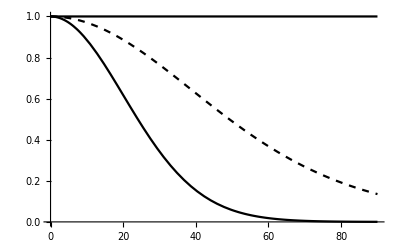

```mathematica
Plot[{p1,p2,hybrid},{θ,0,90},PlotStyle->{Black,Black,{Black,Dashed}}]
```

Hybrids are dashed, average parent is solid:

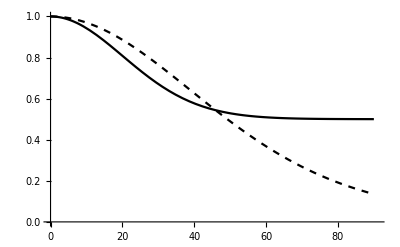

```mathematica
Plot[{(p1+p2)/2,hybrid},{θ,0,90},PlotRange->{{0,91},{0,1}},PlotStyle->{Black,{Black,Dashed}}]
```

This gives the angle, the expectation of the average parent fitness, and the expectation of the hybrid IF the hybrid were an exact mix

```mathematica
Transpose[{θ,(p1+p2)/2,hybrid}/.θ->{0,30,45,90}//N]//MatrixForm
```

(0. | 1. | 1.
30. | 0.671196 | 0.764947
45. | 0.548013 | 0.556668
90. | 0.500168 | 0.135335)

## Figure 4

### (a) (c) Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0},{-2,0,0,0,0,0,0,0,0,0}};
opt2={{2,0,0,0,0,0,0,0,0,0},{√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{√2,-√2,0,0,0,0,0,0,0,0},{2,0,0,0,0,0,0,0,0,0}};
scenario={1.1,3.1,3.2,3.3,3.4};
mutsize={0.04,0.08,0.12} ;

data1all={};
data2all={};

For[L=1,L≤5,L++,

J=1;

data1list={};
data2list={};

For[run=0,run<50,run++,
filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];

(*BC1 fitness in opt1*)
BC1fitness1={};
For[i=1,i≤20,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC hybrid*)
BChybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BChybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BChybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BChybrid];
AppendTo[BC1fitness1,Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k]];
];

(*BC1 fitness in opt2*)
BC1fitness2={};
For[i=1,i≤20,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC hybrid*)
BChybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BChybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BChybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BChybrid];
AppendTo[BC1fitness2,Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k]];
];

(*BC2 fitness in opt1*)
BC2fitness1={};
For[i=1,i≤20,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC hybrid*)
BChybrid={};
inter=Intersection[F1hybrid1,mutpop2];
comp=Complement[Union[F1hybrid1,mutpop2],Intersection[F1hybrid1,mutpop2]];
AppendTo[BChybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BChybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BChybrid];
AppendTo[BC2fitness1,Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k]];
];

(*BC2 fitness in opt2*)
BC2fitness2={};
For[i=1,i≤20,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC hybrid*)
BChybrid={};
inter=Intersection[F1hybrid1,mutpop2];
comp=Complement[Union[F1hybrid1,mutpop2],Intersection[F1hybrid1,mutpop2]];
AppendTo[BChybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BChybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BChybrid];
AppendTo[BC2fitness2,Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k]];
];

data1=1/2*(Mean@BC1fitness1-Mean@BC1fitness2-Mean@BC2fitness1+Mean@BC2fitness2);
data2=1/2*(Mean@BC1fitness1-Mean@BC1fitness2-Mean@BC2fitness1+Mean@BC2fitness2)/Mean@BC1fitness1;

AppendTo[data1list,data1];
AppendTo[data2list,data2];

];

AppendTo[data1all,data1list];
AppendTo[data2all,data2list];

];
```

```mathematica
Export["~/Desktop/Figure4_Haploid_a.csv",Prepend[Transpose[{Flatten[data1all],Join[Table["AE_0",{i,1,Length@data1all[[1]],1}],Table["AE_30",{i,1,Length@data1all[[2]],1}],Table["AE_45",{i,1,Length@data1all[[3]],1}],Table["AE_90",{i,1,Length@data1all[[4]],1}],Table["AE_180",{i,1,Length@data1all[[5]],1}]]}],{"Indicator","Environment"}]];

Export["~/Desktop/Figure4_Haploid_c.csv",Prepend[Transpose[{Flatten[data2all],Join[Table["AE_0",{i,1,Length@data2all[[1]],1}],Table["AE_30",{i,1,Length@data2all[[2]],1}],Table["AE_45",{i,1,Length@data2all[[3]],1}],Table["AE_90",{i,1,Length@data2all[[4]],1}],Table["AE_180",{i,1,Length@data2all[[5]],1}]]}],{"Indicator","Environment"}]];
```

### (b) (d) Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0},{-2,0,0,0,0,0,0,0,0,0}};
opt2={{2,0,0,0,0,0,0,0,0,0},{√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{√2,-√2,0,0,0,0,0,0,0,0},{2,0,0,0,0,0,0,0,0,0}};
scenario={1.1,3.1,3.2,3.3,3.4};
mutsize={0.04,0.08,0.12} ;

data1all={};
data2all={};

For[L=1,L≤5,L++,

J=1;

data1list={};
data2list={};

For[run=0,run<50,run++,
filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*BC1 in opt1*)
BC1fitness1={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤40,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness1,Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k]];
];

(*BC1 in opt2*)
BC1fitness2={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤40,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness2,Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k]];
];

(*BC2 fitness in opt1*)
BC2fitness1={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤40,i++,
BC2hybrid={};
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC2hybrid,2*gamete2[[j]]],0.5<=a<1,AppendTo[BC2hybrid,gamete2[[j]]]];
];
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC2hybrid,gamete1[[j]]]];
];
cur=Total[BC2hybrid];
AppendTo[BC2fitness1,Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k]];
];

(*BC2 fitness in opt2*)
BC2fitness2={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤40,i++,
BC2hybrid={};
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC2hybrid,2*gamete2[[j]]],0.5<=a<1,AppendTo[BC2hybrid,gamete2[[j]]]];
];
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC2hybrid,gamete1[[j]]]];
];
cur=Total[BC2hybrid];
AppendTo[BC2fitness2,Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k]];
];

data1=1/2*(Mean@BC1fitness1-Mean@BC1fitness2-Mean@BC2fitness1+Mean@BC2fitness2);
data2=1/2*(Mean@BC1fitness1-Mean@BC1fitness2-Mean@BC2fitness1+Mean@BC2fitness2)/Mean@BC1fitness1;

AppendTo[data1list,data1];
AppendTo[data2list,data2];

];

AppendTo[data1all,data1list];
AppendTo[data2all,data2list];

];
```

```mathematica
Export["~/Desktop/Figure4_Diploid_b.csv",Prepend[Transpose[{Flatten[data1all],Join[Table["AE_0",{i,1,Length@data1all[[1]],1}],Table["AE_30",{i,1,Length@data1all[[2]],1}],Table["AE_45",{i,1,Length@data1all[[3]],1}],Table["AE_90",{i,1,Length@data1all[[4]],1}],Table["AE_180",{i,1,Length@data1all[[5]],1}]]}],{"Indicator","Environment"}]];

Export["~/Desktop/Figure4_Diploid_d.csv",Prepend[Transpose[{Flatten[data2all],Join[Table["AE_0",{i,1,Length@data2all[[1]],1}],Table["AE_30",{i,1,Length@data2all[[2]],1}],Table["AE_45",{i,1,Length@data2all[[3]],1}],Table["AE_90",{i,1,Length@data2all[[4]],1}],Table["AE_180",{i,1,Length@data2all[[5]],1}]]}],{"Indicator","Environment"}]];
```

## Figure 5

### Haploid (all)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
sphere={1,2,5,10};
trait={10,5,2,1};

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤4,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

numsphere=sphere[[J]];
numtrait=trait[[J]];
optrec={};(*fixed optimum*)
For[nums=1,nums≤numsphere,nums++,
opteach={};
For[numt=1,numt≤numtrait,numt++,
If[(nums==1)&&(numt==1),AppendTo[opteach,2],AppendTo[opteach,0]];
];
AppendTo[optrec,opteach]
];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
focaltraitpop1=Drop[Transpose[pop1][[4]],1];
focaltraitpop2=Drop[Transpose[pop2][[4]],1];

(*adaptation phase until mutations at the focal trait with negative coefficient*)
If[Length@slistpop1>Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Length@slistpop1];
If[Length@slistpop2>Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Length@slistpop2];

(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,3}]],1][[1;;If[nummut1*2>Length@slistpop1,Length@slistpop1,nummut1*2];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,3}]],1][[1;;If[nummut2*2>Length@slistpop2,Length@slistpop2,nummut2*2];;1]];


muttemp1={};
muttemp2={};
For[i=1,i≤Length@mutpop1,i++,
AppendTo[muttemp1,Partition[mutpop1[[i]],numtrait]];
];
For[i=1,i≤Length@mutpop2,i++,
AppendTo[muttemp2,Partition[mutpop2[[i]],numtrait]];
];

(*Pop1*)
Pop1offspring={};
inter=Intersection[muttemp1,muttemp1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[muttemp1,muttemp1],Intersection[muttemp1,muttemp1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];

For[i=1,i≤1000,i++,
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[Flatten[Pop1offspring,1]][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[Pop1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp1[[j]]]];
];
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp2[[j]]]];
];
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[F1hybrid][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[F1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[F1fitnessMean,Mean@F1fitness]

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure5_Haploid_all.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]],F1fitnesslist[[4]]],Join[Table["Pop1(1,10)",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1(2,5)",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1(5,2)",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1(10,1)",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["F1(1,10)",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1(2,5)",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1(5,2)",{i,1,Length@F1fitnesslist[[3]],1}],Table["F1(10,1)",{i,1,Length@F1fitnesslist[[4]],1}]]},{"Fitness","Hybrid Type"}]];
```

### Haploid (first half of adaptation)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
sphere={1,2,5,10};
trait={10,5,2,1};

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤4,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

numsphere=sphere[[J]];
numtrait=trait[[J]];
optrec={};(*fixed optimum*)
For[nums=1,nums≤numsphere,nums++,
opteach={};
For[numt=1,numt≤numtrait,numt++,
If[(nums==1)&&(numt==1),AppendTo[opteach,2],AppendTo[opteach,0]];
];
AppendTo[optrec,opteach]
];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
focaltraitpop1=Drop[Transpose[pop1][[4]],1];
focaltraitpop2=Drop[Transpose[pop2][[4]],1];

(*adaptation phase until mutations at the focal trait with negative coefficient*)
If[Length@slistpop1>Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Length@slistpop1];
If[Length@slistpop2>Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Length@slistpop2];

If[EvenQ[nummut1],nummut1=nummut1,nummut1=nummut1+1];
If[EvenQ[nummut2],nummut2=nummut2,nummut2=nummut2+1];

(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,3}]],1][[1;;Round[nummut1*0.5];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,3}]],1][[1;;Round[nummut2*0.5];;1]];
muttemp1={};
muttemp2={};
For[i=1,i≤Length@mutpop1,i++,
AppendTo[muttemp1,Partition[mutpop1[[i]],numtrait]];
];
For[i=1,i≤Length@mutpop2,i++,
AppendTo[muttemp2,Partition[mutpop2[[i]],numtrait]];
];

(*Pop1*)
Pop1offspring={};
inter=Intersection[muttemp1,muttemp1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[muttemp1,muttemp1],Intersection[muttemp1,muttemp1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];

For[i=1,i≤1000,i++,
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[Flatten[Pop1offspring,1]][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[Pop1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp1[[j]]]];
];
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp2[[j]]]];
];
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[F1hybrid][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[F1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[F1fitnessMean,Mean@F1fitness]

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure5_Haploid_adaptation_first.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]],F1fitnesslist[[4]]],Join[Table["Pop1(1,10)",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1(2,5)",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1(5,2)",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1(10,1)",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["F1(1,10)",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1(2,5)",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1(5,2)",{i,1,Length@F1fitnesslist[[3]],1}],Table["F1(10,1)",{i,1,Length@F1fitnesslist[[4]],1}]]},{"Fitness","Hybrid Type"}]];
```

### Haploid (second half of adaptation)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
sphere={1,2,5,10};
trait={10,5,2,1};

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤4,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

numsphere=sphere[[J]];
numtrait=trait[[J]];
optrec={};(*fixed optimum*)
For[nums=1,nums≤numsphere,nums++,
opteach={};
For[numt=1,numt≤numtrait,numt++,
If[(nums==1)&&(numt==1),AppendTo[opteach,2],AppendTo[opteach,0]];
];
AppendTo[optrec,opteach]
];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
focaltraitpop1=Drop[Transpose[pop1][[4]],1];
focaltraitpop2=Drop[Transpose[pop2][[4]],1];

(*adaptation phase until mutations at the focal trait with negative coefficient*)
If[Length@slistpop1>Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Length@slistpop1];
If[Length@slistpop2>Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Length@slistpop2];

If[EvenQ[nummut1],nummut1=nummut1,nummut1=nummut1+1];
If[EvenQ[nummut2],nummut2=nummut2,nummut2=nummut2+1];

(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,3}]],1][[Round[nummut1*0.5];;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,3}]],1][[Round[nummut2*0.5];;nummut2;;1]];

muttemp1={};
muttemp2={};
For[i=1,i≤Length@mutpop1,i++,
AppendTo[muttemp1,Partition[mutpop1[[i]],numtrait]];
];
For[i=1,i≤Length@mutpop2,i++,
AppendTo[muttemp2,Partition[mutpop2[[i]],numtrait]];
];

(*Pop1*)
Pop1offspring={};
inter=Intersection[muttemp1,muttemp1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[muttemp1,muttemp1],Intersection[muttemp1,muttemp1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];

For[i=1,i≤1000,i++,
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[Flatten[Pop1offspring,1]][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[Pop1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp1[[j]]]];
];
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp2[[j]]]];
];
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[F1hybrid][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[F1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[F1fitnessMean,Mean@F1fitness];

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure5_Haploid_adaptation_second.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]],F1fitnesslist[[4]]],Join[Table["Pop1(1,10)",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1(2,5)",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1(5,2)",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1(10,1)",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["F1(1,10)",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1(2,5)",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1(5,2)",{i,1,Length@F1fitnesslist[[3]],1}],Table["F1(10,1)",{i,1,Length@F1fitnesslist[[4]],1}]]},{"Fitness","Hybrid Type"}]];
```

### Haploid (stationary phase)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
sphere={1,2,5,10};
trait={10,5,2,1};

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤4,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

numsphere=sphere[[J]];
numtrait=trait[[J]];
optrec={};(*fixed optimum*)
For[nums=1,nums≤numsphere,nums++,
opteach={};
For[numt=1,numt≤numtrait,numt++,
If[(nums==1)&&(numt==1),AppendTo[opteach,2],AppendTo[opteach,0]];
];
AppendTo[optrec,opteach]
];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
focaltraitpop1=Drop[Transpose[pop1][[4]],1];
focaltraitpop2=Drop[Transpose[pop2][[4]],1];

(*adaptation phase until mutations at the focal trait with negative coefficient*)
If[Length@slistpop1>Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Length@slistpop1];
If[Length@slistpop2>Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Length@slistpop2];

(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,3}]],1][[nummut1;;If[nummut1*2>Length@slistpop1,Length@slistpop1,nummut1*2];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,3}]],1][[nummut2;;If[nummut2*2>Length@slistpop2,Length@slistpop2,nummut2*2];;1]];

muttemp1={};
muttemp2={};
For[i=1,i≤Length@mutpop1,i++,
AppendTo[muttemp1,Partition[mutpop1[[i]],numtrait]];
];
For[i=1,i≤Length@mutpop2,i++,
AppendTo[muttemp2,Partition[mutpop2[[i]],numtrait]];
];

(*Pop1*)
Pop1offspring={};
inter=Intersection[muttemp1,muttemp1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[muttemp1,muttemp1],Intersection[muttemp1,muttemp1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];

For[i=1,i≤1000,i++,
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[Flatten[Pop1offspring,1]][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[Pop1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp1[[j]]]];
];
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp2[[j]]]];
];
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[F1hybrid][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[F1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[F1fitnessMean,Mean@F1fitness];

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure5_Haploid_stationary.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]],F1fitnesslist[[4]]],Join[Table["Pop1(1,10)",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1(2,5)",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1(5,2)",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1(10,1)",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["F1(1,10)",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1(2,5)",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1(5,2)",{i,1,Length@F1fitnesslist[[3]],1}],Table["F1(10,1)",{i,1,Length@F1fitnesslist[[4]],1}]]},{"Fitness","Hybrid Type"}]];
```

## Figure 5 (primary vs. pleiotropic effects)

### Haploid (all)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
sphere={1,2,5,10};
trait={10,5,2,1};

ratiolist={};

For[J=1,J≤4,J++,

Pop1fitness={};
F1fitness={};

primaryeffect={};
ratio={};

numsphere=sphere[[J]];
numtrait=trait[[J]];
optrec={};(*fixed optimum*)
For[nums=1,nums≤numsphere,nums++,
opteach={};
For[numt=1,numt≤numtrait,numt++,
If[(nums==1)&&(numt==1),AppendTo[opteach,2],AppendTo[opteach,0]];
];
AppendTo[optrec,opteach]
];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
focaltraitpop1=Drop[Transpose[pop1][[4]],1];
focaltraitpop2=Drop[Transpose[pop2][[4]],1];

(*adaptation phase until mutations at the focal trait with negative coefficient*)
If[Length@slistpop1>Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Length@slistpop1];
If[Length@slistpop2>Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Length@slistpop2];

(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,3}]],1][[1;;If[nummut1*2>Length@slistpop1,Length@slistpop1,nummut1*2];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,3}]],1][[1;;If[nummut2*2>Length@slistpop2,Length@slistpop2,nummut2*2];;1]];


muttemp1={};
muttemp2={};
For[i=1,i≤Length@mutpop1,i++,
AppendTo[muttemp1,Partition[mutpop1[[i]],numtrait]];
];
For[i=1,i≤Length@mutpop2,i++,
AppendTo[muttemp2,Partition[mutpop2[[i]],numtrait]];
];

(*Pop1*)
Pop1offspring={};
inter=Intersection[muttemp1,muttemp1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[muttemp1,muttemp1],Intersection[muttemp1,muttemp1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];

For[i=1,i≤1000,i++,
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[Flatten[Pop1offspring,1]][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[Pop1fitness,Fold[Times,1,fitnesscomp]];
];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp1[[j]]]];
];
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp2[[j]]]];
];
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[F1hybrid][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[F1fitness,Fold[Times,1,fitnesscomp]];
AppendTo[primaryeffect,Exp[-q(EuclideanDistance[cur[[1]][[1]],optrec[[1]][[1]]])^k]];
];
AppendTo[ratio,{Mean[Pop1fitness-primaryeffect],Mean[Pop1fitness-F1fitness]}];

];

AppendTo[ratiolist,ratio];

];
```

```mathematica
Export["~/Desktop/Fig5_ratiolist.dat",ratiolist]
```

~/Desktop/Fig6_ratiolist.dat

```mathematica
PieChart[{Map[Mean,Transpose[ratiolist[[1]]]][[2]]-Map[Mean,Transpose[ratiolist[[1]]]][[1]],Map[Mean,Transpose[ratiolist[[1]]]][[1]]},SectorOrigin->Pi/2,PlotLabel->"(1,10)"]
PieChart[{Map[Mean,Transpose[ratiolist[[2]]]][[2]]-Map[Mean,Transpose[ratiolist[[2]]]][[1]],Map[Mean,Transpose[ratiolist[[2]]]][[1]]},SectorOrigin->Pi/2,PlotLabel->"(2,5)"]
PieChart[{Map[Mean,Transpose[ratiolist[[3]]]][[2]]-Map[Mean,Transpose[ratiolist[[3]]]][[1]],Map[Mean,Transpose[ratiolist[[3]]]][[1]]},SectorOrigin->Pi/2,PlotLabel->"(5,2)"]
PieChart[{Map[Mean,Transpose[ratiolist[[4]]]][[2]]-Map[Mean,Transpose[ratiolist[[4]]]][[1]],Map[Mean,Transpose[ratiolist[[4]]]][[1]]},SectorOrigin->Pi/2,PlotLabel->"(10,1)"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*pleiotropic, primary*)
{Map[Mean,Transpose[ratiolist[[4]]]][[2]]-Map[Mean,Transpose[ratiolist[[4]]]][[1]],Map[Mean,Transpose[ratiolist[[4]]]][[1]]}
```

{0.0121304,0.0969631}

## Figure 6

## (a~c) Mutation-order & hybrid speciation (stationary)

```mathematica
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop2_0.dat"];
```

```mathematica
q=1;
k=2;
opt={0,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[nummut1/2;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[nummut2/2;;nummut2;;1]];
```

```mathematica
F1fitness={};
F1phenotype={};
For[i=1,i≤1000,i++,
F1hybrid={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];(*alleles from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];(*alleles from population 2*)
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
AppendTo[F1phenotype,cur];
];
```

```mathematica
Pop1phenotype=Total[mutpop1];
Pop2phenotype=Total[mutpop2];
```

```mathematica
F1phenotype2dimension={};
For[i=1,i≤Length@F1phenotype,i++,
AppendTo[F1phenotype2dimension,F1phenotype[[i]][[1;;2;;1]]];
];
```

```mathematica
λ=5;
Parameters={};
HybridMeanEP={};
ParentMeanEP={};
For[a=-2, a<2, a=a+0.02,
For[b=-2,b<2, b=b+0.02,
AppendTo[Parameters,{a,b}];
opt={a,b,0,0,0,0,0,0,0,0};
EPlist={}; (*establishment probability*)
For[i=1,i≤Length@F1phenotype,i++,
w=Exp[-q(EuclideanDistance[F1phenotype[[i]],opt])^k];
AppendTo[EPlist,(w λ+ProductLog[-ⅇ^(-w λ) w λ])/(w λ)];
];
AppendTo[HybridMeanEP,Mean[EPlist]];
w1=Exp[-q(EuclideanDistance[Pop1phenotype,opt])^k];
w2=Exp[-q(EuclideanDistance[Pop2phenotype,opt])^k];
AppendTo[ParentMeanEP,1/2(w1 λ+ProductLog[-ⅇ^(-w1 λ) w1 λ])/(w1 λ)+1/2(w2 λ+ProductLog[-ⅇ^(-w2 λ) w2 λ])/(w2 λ)];
];
];
```

```mathematica
Parentmax=Table[Max[ParentMeanEP[[i]],10^-6],{i,1,Length[ParentMeanEP]}];
ParentFinalEPPlot=Join[Parameters,Partition[Parentmax,1],2];
Show[ListDensityPlot[ParentFinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"]),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[{Pop1phenotype[[1;;2;;1]],Pop2phenotype[[1;;2;;1]]},PlotStyle->{Red, PointSize[0.03]}]]
```

-Graphics-

```mathematica
Hybridmax=Table[Max[HybridMeanEP[[i]],10^-6],{i,1,Length[ParentMeanEP]}];
HybridFinalEPPlot=Join[Parameters,Partition[Hybridmax,1],2];
Show[ListDensityPlot[HybridFinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"]),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[F1phenotype2dimension,PlotRange->All,PlotStyle->{Black,PointSize[0.01]}]]
```

-Graphics-

```mathematica
maxratio=Table[Max[1,Max[HybridMeanEP[[i]],10^-6]/Max[ParentMeanEP[[i]],10^-6]],{i,1,Length[HybridMeanEP]}];FinalEPPlot=Join[Parameters,Partition[Log[10,maxratio],1],2];
Show[ListDensityPlot[FinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"][#/5]&),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[F1phenotype2dimension,PlotRange->All,PlotStyle->{Black}],
ListPlot[{Pop1phenotype[[1;;2;;1]],Pop2phenotype[[1;;2;;1]]},PlotStyle->{Red, PointSize[0.03]}]]
```

-Graphics-

## (d~f) Mutation-order & hybrid speciation

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[1-p==Exp[-p(λ*w)],p]
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{p→(w λ+ProductLog[-ⅇ^(-w λ) w λ])/(w λ)}}

```mathematica
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop2_0.dat"];
```

```mathematica
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];
```

```mathematica
Pop1phenotype=Total[mutpop1];
Pop2phenotype=Total[mutpop2];
```

```mathematica
F1fitness={};
F1phenotype={};
For[i=1,i≤1000,i++,
F1hybrid={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];(*alleles from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];(*alleles from population 2*)
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
AppendTo[F1phenotype,cur];
];
```

```mathematica
F1phenotype2dimension={};
For[i=1,i≤Length@F1phenotype,i++,
AppendTo[F1phenotype2dimension,F1phenotype[[i]][[1;;2;;1]]];
];
```

```mathematica
λ=5;
Parameters={};
HybridMeanEP={};
ParentMeanEP={};
For[a=0, a<4, a=a+0.02,
For[b=-2,b<2, b=b+0.02,
AppendTo[Parameters,{a,b}];
opt={a,b,0,0,0,0,0,0,0,0};
EPlist={}; (*establishment probability*)
For[i=1,i≤Length@F1phenotype,i++,
w=Exp[-q(EuclideanDistance[F1phenotype[[i]],opt])^k];
AppendTo[EPlist,(w λ+ProductLog[-ⅇ^(-w λ) w λ])/(w λ)];
];
AppendTo[HybridMeanEP,Mean[EPlist]];
w1=Exp[-q(EuclideanDistance[Pop1phenotype,opt])^k];
w2=Exp[-q(EuclideanDistance[Pop2phenotype,opt])^k];
AppendTo[ParentMeanEP,1/2(w1 λ+ProductLog[-ⅇ^(-w1 λ) w1 λ])/(w1 λ)+1/2(w2 λ+ProductLog[-ⅇ^(-w2 λ) w2 λ])/(w2 λ)];
];
];
```

```mathematica
Parentmax=Table[Max[ParentMeanEP[[i]],10^-6],{i,1,Length[ParentMeanEP]}];
ParentFinalEPPlot=Join[Parameters,Partition[Parentmax,1],2];
Show[ListDensityPlot[ParentFinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"]),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[{Pop1phenotype[[1;;2;;1]],Pop2phenotype[[1;;2;;1]]},PlotStyle->{Red, PointSize[0.03]}]]
```

-Graphics-

```mathematica
Hybridmax=Table[Max[HybridMeanEP[[i]],10^-6],{i,1,Length[ParentMeanEP]}];
HybridFinalEPPlot=Join[Parameters,Partition[Hybridmax,1],2];
Show[ListDensityPlot[HybridFinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"]),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[F1phenotype2dimension,PlotRange->All,PlotStyle->{Black,PointSize[0.01]}]]
```

-Graphics-

```mathematica
maxratio=Table[Max[1,Max[HybridMeanEP[[i]],10^-6]/Max[ParentMeanEP[[i]],10^-6]],{i,1,Length[HybridMeanEP]}];
FinalEPPlot=Join[Parameters,Partition[Log[10,maxratio],1],2];
Show[ListDensityPlot[FinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"][#/5]&),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[F1phenotype2dimension,PlotRange->All,PlotStyle->{Black}],
ListPlot[{Pop1phenotype[[1;;2;;1]],Pop2phenotype[[1;;2;;1]]},PlotStyle->{Red, PointSize[0.03]}]]
```

-Graphics-

## (g~i) Ecological & hybrid speciation

```mathematica
Clear["Global`*"]
```

```mathematica
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Haploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Haploid_r=0.04_pop2_0.dat"];
```

```mathematica
q=1;
k=2;
opt1={-√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum1*)
opt2={√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum2*)
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];
```

```mathematica
F1fitness={};
F1phenotype={};
For[i=1,i≤1000,i++,
F1hybrid={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];(*alleles from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];(*alleles from population 2*)
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];(*Calculating fitness of F1*)
AppendTo[F1phenotype,cur];
];
```

```mathematica
Pop1phenotype=Total[mutpop1];
Pop2phenotype=Total[mutpop2];
```

```mathematica
F1phenotype2dimension={};
For[i=1,i≤Length@F1phenotype,i++,
AppendTo[F1phenotype2dimension,F1phenotype[[i]][[1;;2;;1]]];
];
```

```mathematica
λ=5;
Parameters={};
HybridMeanEP={};
ParentMeanEP={};
For[a=-2, a<2, a=a+0.02,
For[b=-4.0,b<0.0, b=b+0.02,
AppendTo[Parameters,{a,b}];
opt={a,b,0,0,0,0,0,0,0,0};
EPlist={}; (*establishment probability*)
For[i=1,i≤Length@F1phenotype,i++,
w=Exp[-q(EuclideanDistance[F1phenotype[[i]],opt])^k];
AppendTo[EPlist,(w λ+ProductLog[-ⅇ^(-w λ) w λ])/(w λ)];
];
AppendTo[HybridMeanEP,Mean[EPlist]];
w1=Exp[-q(EuclideanDistance[Pop1phenotype,opt])^k];
w2=Exp[-q(EuclideanDistance[Pop2phenotype,opt])^k];
AppendTo[ParentMeanEP,1/2(w1 λ+ProductLog[-ⅇ^(-w1 λ) w1 λ])/(w1 λ)+1/2(w2 λ+ProductLog[-ⅇ^(-w2 λ) w2 λ])/(w2 λ)];
];
];
```

```mathematica
Parentmax=Table[Max[ParentMeanEP[[i]],10^-6],{i,1,Length[ParentMeanEP]}];
ParentFinalEPPlot=Join[Parameters,Partition[Parentmax,1],2];
Show[ListDensityPlot[ParentFinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"]),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[{Pop1phenotype[[1;;2;;1]],Pop2phenotype[[1;;2;;1]]},PlotStyle->{Red, PointSize[0.03]}]]
```

-Graphics-

```mathematica
Hybridmax=Table[Max[HybridMeanEP[[i]],10^-6],{i,1,Length[ParentMeanEP]}];
HybridFinalEPPlot=Join[Parameters,Partition[Hybridmax,1],2];
Show[ListDensityPlot[HybridFinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"]),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[F1phenotype2dimension,PlotRange->All,PlotStyle->{Black,PointSize[0.01]}]]
```

-Graphics-

```mathematica
maxratio=Table[Max[1,Max[HybridMeanEP[[i]],10^-6]/Max[ParentMeanEP[[i]],10^-6]],{i,1,Length[HybridMeanEP]}];FinalEPPlot=Join[Parameters,Partition[Log[10,maxratio],1],2];
Show[ListDensityPlot[FinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"][#/5]&),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[F1phenotype2dimension,PlotRange->All,PlotStyle->{Black,PointSize[0.01]}],
ListPlot[{Pop1phenotype[[1;;2;;1]],Pop2phenotype[[1;;2;;1]]},PlotStyle->{Red, PointSize[0.03]}]]
```

-Graphics-

## Figure S1

## Mutation size with fixations

```mathematica
mutsizelist=Import["~/Desktop/FGM-master/Data sets/Figure 2/FGM_multiple100_mut=0.04_N=2000_r.dat"];
ListLinePlot[{Map[Mean,Transpose@mutsizelist],
Map[Min,Transpose@mutsizelist],
Map[Max,Transpose@mutsizelist]},PlotJoined->True,PlotRange->All,Filling->{2->{3}}]
```

-Graphics-

## Selection coefficient with fixations

```mathematica
selcoefflist=Import["~/Desktop/FGM-master/Data sets/Figure 2/FGM_multiple100_mut=0.04_N=2000_s.dat"];
ListLinePlot[{Map[Mean,Transpose@selcoefflist],
Map[Min,Transpose@selcoefflist],
Map[Max,Transpose@selcoefflist]},PlotJoined->True,PlotRange->{{0,120},{-0.001,0.001}},Filling->{2->{3}}]
```

-Graphics-

```mathematica
Length@selcoefflist
```

100

```mathematica
adaptationphase={};
For[i=1,i<=Length@selcoefflist,i++,
AppendTo[adaptationphase,Length@TakeWhile[Sign[selcoefflist[[i]]],#>0.5&]];
];
```

```mathematica
adaptationphase
```

{82,92,87,94,96,66,87,81,102,94,76,94,97,80,80,82,86,71,72,88,98,93,72,74,71,73,75,90,89,86,84,91,74,88,81,113,73,79,105,78,101,86,88,82,86,97,91,87,99,82,86,84,93,89,77,87,81,89,87,79,105,86,84,87,98,91,83,77,68,85,85,78,102,90,89,89,94,77,99,99,80,87,95,92,76,93,77,83,83,97,91,81,120,90,82,82,88,87,93,102}

```mathematica
N@Mean@adaptationphase
```

86.9

## Distance to the optimum along generations

```mathematica
distoptlist=Import["~/Desktop/FGM-master/Data sets/Figure 2/FGM_multiple100_mut=0.04_N=2000_distopt.dat"];
ListLinePlot[{Map[Mean,Transpose@distoptlist],
Map[Min,Transpose@distoptlist],
Map[Max,Transpose@distoptlist]},PlotJoined->True,PlotRange->All,Filling->{2->{3}}]
```

-Graphics-

## Waiting time with fixations

Please use the option “WorkingPrescision” when calculations by “NIntegrate” do not converge.

```mathematica
Clear["Global`*"];
M[w_,s_]:=s w(1-w);
V[w_,n_]:=w (1-w)/n;
G[x_,s_,n_]:=Exp[-Integrate[2 M[x,s]/V[x,n],x]];
u[p_,s_,n_]:=Integrate[G[x,s,n],{x,0,p}]/Integrate[G[x,s,n],{x,0,1}];
ψ[x_,s_,n_]:=2 Integrate[G[x,s,n],{x,0,1}]/(G[x,s,n]*V[x,n]);
T[p_,s_,n_]:=NIntegrate[ψ[ξ,s,n]*u[ξ,s,n](1-u[ξ,s,n]),{ξ,p,1}]+((1-u[p,s,n])/u[p,s,n])NIntegrate[ψ[ξ,s,n]*u[ξ,s,n]*u[ξ,s,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;
opt1={{2,0,0,0,0,0,0,0,0,0}};
opt2={{2,0,0,0,0,0,0,0,0,0}};

scenario={1.1};
mutsize={0.04} ;
imax=10000;
n=2000;
μ=10^(-5);

For[L=1,L≤1,L++,

For[J=1,J≤1,J++,

generations={};
λ=mutsize[[J]];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;120;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;120;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;120;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;120;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];


Waitlist1={};
Waitlist2={};
For[gen=1,gen<Length@phenotype1,gen++,
Problist={};
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt1[[L]]])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];

Waitlist3={};
Waitlist4={};
For[gen=1,gen<Length@phenotype2,gen++,
Problist={};
AppendTo[Waitlist3,T[1/n,slistpop2[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt2[[L]]])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];

(*Number of generations*)
AppendTo[generations,Waitlist1+Waitlist2];
AppendTo[generations,Waitlist3+Waitlist4];

];

];

];
```

```mathematica
maxlist=Accumulate@Map[Max,Transpose[generations]];
minlist=Accumulate@Map[Min,Transpose[generations]];
meanlist=Accumulate@Map[Mean,Transpose[generations]];
ListLogPlot[{meanlist,
minlist,maxlist
},Filling->{2->{3}},Joined->True,AxesOrigin->{1,0}]
```

-Graphics-

## Figure S2

### Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[nummut1;;-1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[nummut2;;-1;;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];

(*F2*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*BC1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

];
```

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

{0.998847,0.731681,0.737916,0.788242}

{1.49955×10^-14,0.101146,0.100326,0.0905563}

{0.998847→1.49955×10^-14,0.731681→0.101146,0.737916→0.100326,0.788242→0.0905563}

```mathematica
Export["~/Desktop/FigureS2_Haploid.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

### Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[nummut1;;-1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[nummut2;;-1;;1]];

(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
 ;];

(*BC1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

];
```

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

{0.999273,0.999784,0.852461,0.921533}

{2.01051×10^-14,2.67698×10^-14,0.0632371,0.0318199}

{0.999273→2.01051×10^-14,0.999784→2.67698×10^-14,0.852461→0.0632371,0.921533→0.0318199}

```mathematica
Export["~/Desktop/FigureS2_Diploid.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

## Figure S3

### F1 fitness relative to “average”parental populations

### (a) Haploid angle=0

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
mutsize={0.04,0.08,0.12} ;

Pop1fitnesslist={};
Pop2fitnesslist={};
F1fitnesslist={};

For[J=1,J≤1,J++,

Pop1fitnessMeanlist={};
Pop2fitnessMeanlist={};
F1fitnessMeanlist={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];


(*Mutations in each population*)
nummut1=120;
nummut2=120;
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
(*Making offsprings*)
Pop1fitnessMean ={};
For[l=1,l≤Length@mutpop1,l++,
Pop1fitness={};

For[i=1,i≤50,i++,
Pop1offspring={};
inter=Intersection[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]],Intersection[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,N[Exp[-q(EuclideanDistance[cur,opt])^k],{Infinity,5}]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];
];
AppendTo[Pop1fitnessMeanlist,Pop1fitnessMean];

(*Pop2*)
(*Making offsprings*)
Pop2fitnessMean ={};
For[l=1,l≤Length@mutpop2,l++,
Pop2fitness={};

For[i=1,i≤50,i++,
Pop2offspring={};
inter=Intersection[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]],Intersection[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]]];(*mutations included in either parent*)
AppendTo[Pop2offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop2offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop2offspring,1]];
AppendTo[Pop2fitness,N[Exp[-q(EuclideanDistance[cur,opt])^k],{Infinity,5}]];
];
AppendTo[Pop2fitnessMean,Mean@Pop2fitness];
];
AppendTo[Pop2fitnessMeanlist,Pop2fitnessMean];

(*F1*)
(*Making offsprings*)
F1fitnessMean ={};
For[l=1,l≤Min[Length@mutpop1,Length@mutpop2],l++,
F1fitness={};

For[i=1,i≤50,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1[[1;;l;;1]],j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2[[1;;l;;1]],j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,N[Exp[-q(EuclideanDistance[cur,opt])^k],{Infinity,5}]];(*Calculating fitness of F1*)
];
AppendTo[F1fitnessMean,Mean@F1fitness];
];
AppendTo[F1fitnessMeanlist,F1fitnessMean];

];

];
```

```mathematica
ListLinePlot[{Map[Mean,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Min,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Max,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])]},PlotJoined->True,PlotRange->{{0,120},{0,1.3}},Filling->{2->{3}}]
```

-Graphics-

```mathematica
ListLinePlot[{Map[Mean,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Min,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Max,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])]},PlotJoined->True,PlotRange->{{0,120},{0.9,1.1}},Filling->{2->{3}}]
```

-Graphics-

```mathematica
list=Map[Mean,Transpose@F1fitnessMeanlist/(Transpose[(1/2)Pop1fitnessMeanlist]+Transpose[(1/2)Pop2fitnessMeanlist])];
position=Flatten[Position[list,Max[list]]][[1]];
```

```mathematica
data=Flatten@Take[Transpose@F1fitnessMeanlist/(Transpose[(1/2)Pop1fitnessMeanlist]+Transpose[(1/2)Pop2fitnessMeanlist]),{position}];
```

```mathematica
TTest[data,1]
```

0.0113155

### (b) Haploid_angle=30

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0}};
scenario={1.1,3.1,3.2,3.3};
mutsize={0.04,0.08,0.12} ;

Pop1fitnesslist={};
Pop2fitnesslist={};
F1fitnesslist={};

L=2;


For[J=1,J≤1,J++,

Pop1fitnessMeanlist={};
Pop2fitnessMeanlist={};
F1fitnessMeanlist={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];


(*Mutations in each population*)
nummut1=120;
nummut2=120;
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
(*Making offsprings*)
Pop1fitnessMean ={};
For[l=1,l≤Length@mutpop1,l++,
Pop1fitness={};

For[i=1,i≤50,i++,
Pop1offspring={};
inter=Intersection[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]],Intersection[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,N[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k],{Infinity,5}]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];
];
AppendTo[Pop1fitnessMeanlist,Pop1fitnessMean];

(*Pop2*)
(*Making offsprings*)
Pop2fitnessMean ={};
For[l=1,l≤Length@mutpop2,l++,
Pop2fitness={};

For[i=1,i≤50,i++,
Pop2offspring={};
inter=Intersection[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]],Intersection[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]]];(*mutations included in either parent*)
AppendTo[Pop2offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop2offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop2offspring,1]];
AppendTo[Pop2fitness,N[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k],{Infinity,5}]];
];
AppendTo[Pop2fitnessMean,Mean@Pop2fitness];
];
AppendTo[Pop2fitnessMeanlist,Pop2fitnessMean];


(*F1*)
(*Making offsprings*)
F1fitnessMean ={};
For[l=1,l≤Min[Length@mutpop1,Length@mutpop2],l++,
F1fitness={};

For[i=1,i≤50,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1[[1;;l;;1]],j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2[[1;;l;;1]],j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,N[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k],{Infinity,5}]];(*Calculating fitness of F1*)
];
AppendTo[F1fitnessMean,Mean@F1fitness];
];
AppendTo[F1fitnessMeanlist,F1fitnessMean];

];

];
```

```mathematica
ListLinePlot[{Map[Mean,Transpose@F1fitnessMeanlist/(Transpose[(1/2)Pop1fitnessMeanlist]+Transpose[(1/2)Pop2fitnessMeanlist])],
Map[Min,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Max,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])]},PlotJoined->True,PlotRange->{{0,120},{0,1.3}},Filling->{2->{3}}]
```

-Graphics-

```mathematica
ListLinePlot[{Map[Mean,Transpose@F1fitnessMeanlist/(Transpose[(1/2)Pop1fitnessMeanlist]+Transpose[(1/2)Pop2fitnessMeanlist])],
Map[Min,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Max,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])]},PlotJoined->True,PlotRange->{{0,120},{0.9,1.1}},Filling->{2->{3}}]
```

-Graphics-

```mathematica
list=Map[Mean,Transpose@F1fitnessMeanlist/(Transpose[(1/2)Pop1fitnessMeanlist]+Transpose[(1/2)Pop2fitnessMeanlist])];
position=Flatten[Position[list,Max[list]]][[1]];
```

```mathematica
data=Flatten@Take[Transpose@F1fitnessMeanlist/(Transpose[(1/2)Pop1fitnessMeanlist]+Transpose[(1/2)Pop2fitnessMeanlist]),{position}];
```

```mathematica
TTest[data,1]
```

0.0024172

### (c) Haploid_angle=45

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0}};
scenario={1.1,3.1,3.2,3.3};
mutsize={0.04,0.08,0.12} ;

Pop1fitnesslist={};
Pop2fitnesslist={};
F1fitnesslist={};

L=3;


For[J=1,J≤1,J++,

Pop1fitnessMeanlist={};
Pop2fitnessMeanlist={};
F1fitnessMeanlist={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];


(*Mutations in each population*)
nummut1=120;
nummut2=120;
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
(*Making offsprings*)
Pop1fitnessMean ={};
For[l=1,l≤Length@mutpop1,l++,
Pop1fitness={};

For[i=1,i≤50,i++,
Pop1offspring={};
inter=Intersection[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]],Intersection[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,N[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k],{Infinity,5}]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];
];
AppendTo[Pop1fitnessMeanlist,Pop1fitnessMean];

(*Pop2*)
(*Making offsprings*)
Pop2fitnessMean ={};
For[l=1,l≤Length@mutpop2,l++,
Pop2fitness={};

For[i=1,i≤50,i++,
Pop2offspring={};
inter=Intersection[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]],Intersection[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]]];(*mutations included in either parent*)
AppendTo[Pop2offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop2offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop2offspring,1]];
AppendTo[Pop2fitness,N[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k],{Infinity,5}]];
];
AppendTo[Pop2fitnessMean,Mean@Pop2fitness];
];
AppendTo[Pop2fitnessMeanlist,Pop2fitnessMean];

(*F1*)
(*Making offsprings*)
F1fitnessMean ={};
For[l=1,l≤Min[Length@mutpop1,Length@mutpop2],l++,
F1fitness={};

For[i=1,i≤50,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1[[1;;l;;1]],j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2[[1;;l;;1]],j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,N[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k],{Infinity,5}]];(*Calculating fitness of F1*)
];
AppendTo[F1fitnessMean,Mean@F1fitness];
];
AppendTo[F1fitnessMeanlist,F1fitnessMean];

];

];
```

```mathematica
ListLinePlot[{Map[Mean,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Min,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Max,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])]},PlotJoined->True,PlotRange->{{0,120},{0,1.3}},Filling->{2->{3}}]
```

-Graphics-

```mathematica
ListLinePlot[{Map[Mean,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Min,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Max,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])]},PlotJoined->True,PlotRange->{{0,120},{0.9,1.1}},Filling->{2->{3}}]
```

-Graphics-

```mathematica
list=Map[Mean,Transpose@F1fitnessMeanlist/(Transpose[(1/2)Pop1fitnessMeanlist]+Transpose[(1/2)Pop2fitnessMeanlist])];
position=Flatten[Position[list,Max[list]]][[1]];
```

```mathematica
data=Flatten@Take[Transpose@F1fitnessMeanlist/(Transpose[(1/2)Pop1fitnessMeanlist]+Transpose[(1/2)Pop2fitnessMeanlist]),{position}];
```

```mathematica
TTest[data,1]
```

0.00808491

### (d) Haploid_angle=90

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0}};
scenario={1.1,3.1,3.2,3.3};
mutsize={0.04,0.08,0.12} ;

Pop1fitnesslist={};
Pop2fitnesslist={};
F1fitnesslist={};

L=4;


For[J=1,J≤1,J++,

Pop1fitnessMeanlist={};
Pop2fitnessMeanlist={};
F1fitnessMeanlist={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];


(*Mutations in each population*)
nummut1=120;
nummut2=120;
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
(*Making offsprings*)
Pop1fitnessMean ={};
For[l=1,l≤Length@mutpop1,l++,
Pop1fitness={};

For[i=1,i≤50,i++,
Pop1offspring={};
inter=Intersection[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]],Intersection[mutpop1[[1;;l;;1]],mutpop1[[1;;l;;1]]]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,N[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k],{Infinity,5}]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];
];
AppendTo[Pop1fitnessMeanlist,Pop1fitnessMean];


(*Pop2*)
(*Making offsprings*)
Pop2fitnessMean ={};
For[l=1,l≤Length@mutpop2,l++,
Pop2fitness={};

For[i=1,i≤50,i++,
Pop2offspring={};
inter=Intersection[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]],Intersection[mutpop2[[1;;l;;1]],mutpop2[[1;;l;;1]]]];(*mutations included in either parent*)
AppendTo[Pop2offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop2offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop2offspring,1]];
AppendTo[Pop2fitness,N[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k],{Infinity,5}]];
];
AppendTo[Pop2fitnessMean,Mean@Pop2fitness];
];
AppendTo[Pop2fitnessMeanlist,Pop2fitnessMean];


(*F1*)
(*Making offsprings*)
F1fitnessMean ={};
For[l=1,l≤Min[Length@mutpop1,Length@mutpop2],l++,
F1fitness={};

For[i=1,i≤50,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1[[1;;l;;1]],j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2[[1;;l;;1]],j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,N[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k],{Infinity,5}]];(*Calculating fitness of F1*)
];
AppendTo[F1fitnessMean,Mean@F1fitness];
];
AppendTo[F1fitnessMeanlist,F1fitnessMean];

];

];
```

```mathematica
ListLinePlot[{Map[Mean,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Min,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Max,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])]},PlotJoined->True,PlotRange->{{0,120},{0,1.3}},Filling->{2->{3}}]
```

-Graphics-

```mathematica
ListLinePlot[{Map[Mean,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Min,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])],
Map[Max,Transpose@F1fitnessMeanlist/((1/2)Transpose[Pop1fitnessMeanlist]+(1/2)Transpose[Pop2fitnessMeanlist])]},PlotJoined->True,PlotRange->{{0,120},{0.9,1.1}},Filling->{2->{3}}]
```

-Graphics-

```mathematica
list=Map[Mean,Transpose@F1fitnessMeanlist/(Transpose[(1/2)Pop1fitnessMeanlist]+Transpose[(1/2)Pop2fitnessMeanlist])];
position=Flatten[Position[list,Max[list]]][[1]];
```

```mathematica
data=Flatten@Take[Transpose@F1fitnessMeanlist/(Transpose[(1/2)Pop1fitnessMeanlist]+Transpose[(1/2)Pop2fitnessMeanlist]),{position}];
```

```mathematica
TTest[data,1]
```

0.433029

## Figure S4

Throughout, we use α = 2 in equation (1), reflecting the Gaussian fitness function that we used in the simulation.

```mathematica
α=2;
```

Alternatively, one could fit α to the data as well, given enough types of crosses.

### Applying equation (6) from Simon et al. (2018) to Figure 3a

```mathematica
type={P1 ,BC,F1,F2,P2};
fit={0.9988468152503241,0.788241794332467,0.7316806440331325,0.7379159695942803,0.9969461042736024};
hvec={0,0.25,0.5,0.5,1};
```

```mathematica
breakdown=(-Log[fit])^(2/α)
```

{0.00115385,0.23795,0.312411,0.303925,0.00305857}

In this case (with both parents having high fitness), the worst genotype should be F1 (i.e., an individual with h=1/2).

```mathematica
worstS=breakdown[[3]];
```

```mathematica
breakdown=breakdown/worstS;
```

```mathematica
eqnA7=h (1-h)+((1-h)^2 fP1+(h)^2 fP2)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

0.00369337 (1-h)^2+(1-h) h+0.0097902 h^2

```mathematica
predict=Table[eqnA7/.h->hvec[[i]],{i,1,Length[type]}]
```

{0.00369337,0.190189,0.253371,0.253371,0.0097902}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict=Exp[-predict*worstS]
```

{0.998847,0.942313,0.923896,0.923896,0.996946}

```mathematica
ticktab=Table[{i,type[[i]]},{i,1,Length[type]}]
```

{{1,P1},{2,BC},{3,F1},{4,F2},{5,P2}}

This doesn’t fit very well because eqnA7 gives h (1-h) in this case, and there might be a 4 missing in equation (A7)???

```mathematica
eqnA7alt=4h (1-h)+((1-h)^2 fP1+(h)^2 fP2)/.fP1->First[breakdown]/.fP2->Last[breakdown]
predictalt=Table[eqnA7alt/.h->hvec[[i]],{i,1,Length[type]}];
fitpredictalt=Exp[-predictalt*worstS];
```

0.00369337 (1-h)^2+4 (1-h) h+0.0097902 h^2

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->{Black,PointSize[0.03]}],
ListPlot[fitpredict,Joined->True,PlotStyle->Dashed],
ListPlot[fitpredictalt,Joined->True,PlotStyle->{Thin},PlotMarkers->{Style["×",30]}],
PlotRange->All
]
```

-Graphics-

Here we have used information from P1, P2, and F1, obtaining BC and F2 for free.  We could also find the best estimator of the reference value for E(S†), refS, by minimizing the sum of squared deviations between the observed and predicted fitnesses:

```mathematica
breakdown=-Log[fit]/refS;
```

```mathematica
eqn6=fP1+β1 h (1-β2 h)-p12/.β1->4-2fP1/.β2->(4-fP1-fP2)/(4-2 fP1)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

-p12+h (1-(h (4-0.00421242/refS))/(4-0.0023077/refS)) (4-0.0023077/refS)+0.00115385/refS

```mathematica
predict=Table[eqnA7/.h->hvec[[i]],{i,1,Length[type]}]
```

{0.00369337,0.190189,0.253371,0.253371,0.0097902}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict=Exp[-predict*refS]
```

{ⅇ^(-0.00369337 refS),ⅇ^(-0.190189 refS),ⅇ^(-0.253371 refS),ⅇ^(-0.253371 refS),ⅇ^(-0.0097902 refS)}

Minimizing the sum of squared deviations between the expected and observed fitness for the unused data (i.e., not the two parentals) gives:

```mathematica
Sum[(fit[[i]]-fitpredict[[i]])^2,{i,2,Length[fitpredict]-1}];
```

```mathematica
estrefS=Minimize[%,refS]
```

{0.0000401619,{refS→1.22485}}

The estimated worst breakdown (refS) is very close the four times the breakdown used, consistent with a four missing in equation (A7):

```mathematica
4 worstS
```

1.24964

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->{Black,PointSize[0.03]}],
ListPlot[fitpredict/.estrefS[[2]],Joined->True,PlotStyle->{Dashed,Gray}],ListPlot[fitpredictalt,PlotMarkers->{Style["×",30]},PlotStyle->Orange],PlotRange->All
]
```

-Graphics-

Here we have used information from P1, P2, and estimated one free parameter from F2, BC and F1.

### Applying equation (6) from Simon et al. (2018) to Figure 3b

```mathematica
type={P1 ,BC,F1,F2,P2};
fit={0.9992727156167194,0.9215334286021335,0.9997841122345499,0.8524612947429417,0.9937408265484922};
hvec={0,0.25,0.5,0.5,1};
p12vec={0,0.5,1,0.5,0};
```

```mathematica
breakdown=(-Log[fit])^(2/α)
```

{0.000727549,0.0817162,0.000215911,0.159627,0.00627884}

In this case (with both parents having high fitness), the worst genotype should be F∞ (i.e., an individual with h=1/2 and p12=0), given by the black curve below (from equation (9)):

```mathematica
Show[
Plot[4 (1-h) h-p12/.p12->0,{h,0,1},PlotStyle->Black],
Plot[4 (1-h) h-p12/.p12->0.5,{h,0,1},PlotStyle->Red],
PlotRange->All,
AxesLabel->{"h","breakdown"}
]
```

-Graphics-

F2 has only half of the heterozgosity and so should have half the breakdown (red above).  We thus use double this breakdown to estimate the worst genotype:

```mathematica
worstS=2 breakdown[[4]];
```

```mathematica
breakdown=breakdown/worstS;
```

```mathematica
eqn6=fP1+β1 h (1-β2 h)-p12/.β1->4-2fP1/.β2->(4-fP1-fP2)/(4-2 fP1)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

0.0022789+3.99544 (1-0.995648 h) h-p12

```mathematica
predict=Table[eqn6/.h->hvec[[i]]/.p12->p12vec[[i]],{i,1,Length[type]}]
```

{0.0022789,0.252511,0.00548652,0.505487,0.0196672}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict1=Exp[-predict*worstS]
```

{0.999273,0.922548,0.99825,0.850969,0.993741}

```mathematica
ticktab=Table[{i,type[[i]]},{i,1,Length[type]}]
```

{{1,P1},{2,BC},{3,F1},{4,F2},{5,P2}}

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->PointSize[0.02]],
ListPlot[fitpredict1,Joined->True,PlotStyle->Dashed],PlotRange->All
]
```

-Graphics-

Here we have used information from P1, P2, and F2, obtaining BC and F1 for free.  We could also find the best estimator of the reference value for E(S†), refS, by minimizing the sum of squared deviations between the observed and predicted fitnesses:

```mathematica
breakdown=-Log[fit]/refS;
```

```mathematica
eqn6=fP1+β1 h (1-β2 h)-p12/.β1->4-2fP1/.β2->(4-fP1-fP2)/(4-2 fP1)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

-p12+h (1-(h (4-0.00700639/refS))/(4-0.0014551/refS)) (4-0.0014551/refS)+0.000727549/refS

```mathematica
predict=Table[eqn6/.h->hvec[[i]]/.p12->p12vec[[i]],{i,1,Length[type]}]
```

{0.000727549/refS,-0.5+0.25 (1-(0.25 (4-0.00700639/refS))/(4-0.0014551/refS)) (4-0.0014551/refS)+0.000727549/refS,-1+0.5 (1-(0.5 (4-0.00700639/refS))/(4-0.0014551/refS)) (4-0.0014551/refS)+0.000727549/refS,-0.5+0.5 (1-(0.5 (4-0.00700639/refS))/(4-0.0014551/refS)) (4-0.0014551/refS)+0.000727549/refS,(1-(4-0.00700639/refS)/(4-0.0014551/refS)) (4-0.0014551/refS)+0.000727549/refS}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict=Exp[-predict*refS]
```

{0.999273,ⅇ^((0.5-0.25 (1-(0.25 (4-0.00700639/refS))/(4-0.0014551/refS)) (4-0.0014551/refS)-0.000727549/refS) refS),ⅇ^((1-0.5 (1-(0.5 (4-0.00700639/refS))/(4-0.0014551/refS)) (4-0.0014551/refS)-0.000727549/refS) refS),ⅇ^((0.5-0.5 (1-(0.5 (4-0.00700639/refS))/(4-0.0014551/refS)) (4-0.0014551/refS)-0.000727549/refS) refS),ⅇ^((-(1-(4-0.00700639/refS)/(4-0.0014551/refS)) (4-0.0014551/refS)-0.000727549/refS) refS)}

Minimizing the sum of squared deviations between the expected and observed fitness for the unused data (i.e., not the two parentals) gives:

```mathematica
Sum[(fit[[i]]-fitpredict[[i]])^2,{i,2,Length[fitpredict]-1}];
```

```mathematica
estrefS=Minimize[%,refS]
```

{4.92396×10^-6,{refS→0.317544}}

The estimated worst breakdown (refS) is very close the the breakdown used (twice the breakdown in the F2):

```mathematica
worstS
```

0.319255

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->{Black,PointSize[0.03]}],
ListPlot[fitpredict/.estrefS[[2]],Joined->True,PlotStyle->{Dashed,Gray}],ListPlot[fitpredict1,PlotMarkers->{Style["×",30]},PlotStyle->Orange],PlotRange->All
]
```

-Graphics-

Here we have used information from P1, P2, and estimated one free parameter from F2, BC and F1.

### Applying equation (6) from Simon et al. (2018) to Figure S3a

```mathematica
type={P1 ,BCL,F1,F2,BCF,P2};
fit={0.9987279326140621,0.7614728144448577,0.583915342910723,0.5802130477149897,0.45980625479190135,0.3502099204234103};
hvec={0,0.25,0.5,0.5,0.75,1};
```

```mathematica
breakdown=(-Log[fit])^(2/α)
```

{0.00127288,0.272501,0.537999,0.54436,0.77695,1.04922}

In this case (with only one parent having low fitness), the worst genotype should be BCF∞ (i.e., an individual with h near 1).

```mathematica
worstS=Last[breakdown];
```

```mathematica
breakdown=breakdown/worstS;
```

```mathematica
eqnA7=h (1-h)+((1-h)^2 fP1+(h)^2 fP2)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

0.00121316 (1-h)^2+(1-h) h+1. h^2

```mathematica
predict=Table[eqnA7/.h->hvec[[i]],{i,1,Length[type]}]
```

{0.00121316,0.250682,0.500303,0.500303,0.750076,1.}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict1=Exp[-predict*worstS]
```

{0.998728,0.768725,0.591597,0.591597,0.45521,0.35021}

```mathematica
{0.9987279326140621,0.7687252724402345,0.5915970792968452,0.5915970792968452,0.4552099883852243,0.3502099204234103}
```

```mathematica
ticktab=Table[{i,type[[i]]},{i,1,Length[type]}]
```

{{1,P1},{2,BCL},{3,F1},{4,F2},{5,BCF},{6,P2}}

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->PointSize[0.02]],
ListPlot[fitpredict,Joined->True,PlotStyle->Dashed]
]
```

-Graphics-

Here we have only used information from P1, P2, and obtained the remaining crosses from this information (using P2 as the estimated worst fitness). We could also find the best estimator of the reference value for E(S†), refS, by minimizing the sum of squared deviations between the observed and predicted fitnesses:

```mathematica
breakdown=-Log[fit]/refS;
```

```mathematica
eqnA7=h (1-h)+((1-h)^2 fP1+(h)^2 fP2)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

(1-h) h+(0.00127288 (1-h)^2)/refS+(1.04922 h^2)/refS

```mathematica
predict=Table[eqnA7/.h->hvec[[i]],{i,1,Length[type]}]
```

{0.+0.00127288/refS,0.1875+0.0662924/refS,0.25+0.262624/refS,0.25+0.262624/refS,0.1875+0.590267/refS,0.+1.04922/refS}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict=Exp[-predict*refS]
```

{ⅇ^((0.-0.00127288/refS) refS),ⅇ^((-0.1875-0.0662924/refS) refS),ⅇ^((-0.25-0.262624/refS) refS),ⅇ^((-0.25-0.262624/refS) refS),ⅇ^((-0.1875-0.590267/refS) refS),ⅇ^((0.-1.04922/refS) refS)}

Minimizing the sum of squared deviations between the expected and observed fitness for the unused data (i.e., not the two parentals) gives:

```mathematica
Sum[(fit[[i]]-fitpredict[[i]])^2,{i,2,Length[fitpredict]-1}];
```

```mathematica
estrefS=Minimize[%,refS]
```

{0.0000944758,{refS→1.09782}}

The estimated worst breakdown (refS = 1.28979) is close to the breakdown used above (1.20397, assuming the worst hybrid was BCF∞, close to parent 2).

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->PointSize[0.02]],
ListPlot[fitpredict/.estrefS[[2]],Joined->True,PlotStyle->Dashed],PlotRange->All
]
```

-Graphics-

Here we have used information from P1, P2, and estimated one free parameter from BCL, F1, F2, and BCF.

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->{Black,PointSize[0.03]}],
ListPlot[fitpredict/.estrefS[[2]],Joined->True,PlotStyle->{Dashed,Gray}],ListPlot[fitpredict1,PlotMarkers->{Style["×",30]},PlotStyle->Orange],PlotRange->All
]
```

-Graphics-

### Applying equation (6) from Simon et al. (2018) to Figure S3b

```mathematica
type={P1 ,BCL,F1,F2,BCF,P2};
fit={0.9987411106176619,0.8470674491130437,0.7563141588270936,0.658694546133725,0.5443337862170552,0.3422039900352162};
hvec={0,0.25,0.5,0.5,0.75,1};
p12vec={0,0.5,1,0.5,0.5,0};
```

```mathematica
breakdown=(-Log[fit])^(2/α)
```

{0.00125968,0.165975,0.279298,0.417495,0.608193,1.07235}

In this case (with only one parent having low fitness), the worst genotype should be BCF∞ (i.e., an individual with h near 1).

```mathematica
worstS=Last[breakdown];
```

```mathematica
breakdown=breakdown/worstS;
```

```mathematica
eqn6=fP1+β1 h (1-β2 h)-p12/.β1->4-2fP1/.β2->(4-fP1-fP2)/(4-2 fP1)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

0.0011747+3.99765 (1-0.750147 h) h-p12

```mathematica
predict=Table[eqn6/.h->hvec[[i]]/.p12->p12vec[[i]],{i,1,Length[type]}]
```

{0.0011747,0.313161,0.250294,0.750294,0.812573,1.}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict1=Exp[-predict*worstS]
```

{0.998741,0.714754,0.7646,0.447277,0.418381,0.342204}

```mathematica
ticktab=Table[{i,type[[i]]},{i,1,Length[type]}]
```

{{1,P1},{2,BCL},{3,F1},{4,F2},{5,BCF},{6,P2}}

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->PointSize[0.02]],
ListPlot[fitpredict1,Joined->True,PlotStyle->Dashed]
]
```

-Graphics-

Here we have only used information from P1, P2, and obtained the remaining crosses from this information (using P2 as the estimated worst fitness). We could also find the best estimator of the reference value for E(S†), refS, by minimizing the sum of squared deviations between the observed and predicted fitnesses:

```mathematica
breakdown=-Log[fit]/refS;
```

```mathematica
eqn6=fP1+β1 h (1-β2 h)-p12/.β1->4-2fP1/.β2->(4-fP1-fP2)/(4-2 fP1)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

-p12+h (1-(h (4-1.07361/refS))/(4-0.00251936/refS)) (4-0.00251936/refS)+0.00125968/refS

```mathematica
predict=Table[eqn6/.h->hvec[[i]]/.p12->p12vec[[i]],{i,1,Length[type]}]
```

{0.00125968/refS,-0.5+0.25 (1-(0.25 (4-1.07361/refS))/(4-0.00251936/refS)) (4-0.00251936/refS)+0.00125968/refS,-1+0.5 (1-(0.5 (4-1.07361/refS))/(4-0.00251936/refS)) (4-0.00251936/refS)+0.00125968/refS,-0.5+0.5 (1-(0.5 (4-1.07361/refS))/(4-0.00251936/refS)) (4-0.00251936/refS)+0.00125968/refS,-0.5+0.75 (1-(0.75 (4-1.07361/refS))/(4-0.00251936/refS)) (4-0.00251936/refS)+0.00125968/refS,(1-(4-1.07361/refS)/(4-0.00251936/refS)) (4-0.00251936/refS)+0.00125968/refS}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict=Exp[-predict*refS]
```

{0.998741,ⅇ^((0.5-0.25 (1-(0.25 (4-1.07361/refS))/(4-0.00251936/refS)) (4-0.00251936/refS)-0.00125968/refS) refS),ⅇ^((1-0.5 (1-(0.5 (4-1.07361/refS))/(4-0.00251936/refS)) (4-0.00251936/refS)-0.00125968/refS) refS),ⅇ^((0.5-0.5 (1-(0.5 (4-1.07361/refS))/(4-0.00251936/refS)) (4-0.00251936/refS)-0.00125968/refS) refS),ⅇ^((0.5-0.75 (1-(0.75 (4-1.07361/refS))/(4-0.00251936/refS)) (4-0.00251936/refS)-0.00125968/refS) refS),ⅇ^((-(1-(4-1.07361/refS)/(4-0.00251936/refS)) (4-0.00251936/refS)-0.00125968/refS) refS)}

Minimizing the sum of squared deviations between the expected and observed fitness for the unused data (i.e., not the two parentals) gives:

```mathematica
Sum[(fit[[i]]-fitpredict[[i]])^2,{i,2,Length[fitpredict]-1}];
```

```mathematica
estrefS=Minimize[%,refS]
```

{0.00182138,{refS→0.296776}}

The estimated worst breakdown (refS = 0.329008) is now very far the breakdown used above (assuming the worst hybrid was BCF∞, close to parent 2) but closer to the breakdown observed in F1 hybrids (0.314711).  This gives an excellent fit to the data:

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->PointSize[0.02]],
ListPlot[fitpredict/.estrefS[[2]],Joined->True,PlotStyle->Dashed],PlotRange->All
]
```

-Graphics-

Here we have used information from P1, P2, and estimated one free parameter from BCL, F1, F2, and BCF.

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->{Black,PointSize[0.03]}],
ListPlot[fitpredict/.estrefS[[2]],Joined->True,PlotStyle->{Dashed,Gray}],ListPlot[fitpredict1,PlotMarkers->{Style["×",30]},PlotStyle->Orange],PlotRange->All
]
```

-Graphics-

### Applying equation (6) from Simon et al. (2018) to Figure S3c

```mathematica
type={P1 ,BCL,F1,F2,BCF,P2};
fit={0.9991122127658826,0.5012092952767659,0.12647282419056557,0.12138872700053983,0.010842685275671062,0.00037572976257593165};
hvec={0,0.25,0.5,0.5,0.75,1};
```

```mathematica
breakdown=(-Log[fit])^(2/α)
```

{0.000888182,0.690732,2.06773,2.10876,4.52426,7.88664}

In this case (with only one parent having low fitness), the worst genotype should be BCF∞ (i.e., an individual with h near 1).

```mathematica
worstS=Last[breakdown];
```

```mathematica
breakdown=breakdown/worstS;
```

```mathematica
eqnA7=h (1-h)+((1-h)^2 fP1+(h)^2 fP2)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

0.000112618 (1-h)^2+(1-h) h+1. h^2

```mathematica
predict=Table[eqnA7/.h->hvec[[i]],{i,1,Length[type]}]
```

{0.000112618,0.250063,0.500028,0.500028,0.750007,1.}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict1=Exp[-predict*worstS]
```

{0.999112,0.139156,0.0193794,0.0193794,0.00269856,0.00037573}

```mathematica
ticktab=Table[{i,type[[i]]},{i,1,Length[type]}]
```

{{1,P1},{2,BCL},{3,F1},{4,F2},{5,BCF},{6,P2}}

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->PointSize[0.02]],
ListPlot[fitpredict1,Joined->True,PlotStyle->Dashed]
]
```

-Graphics-

Here we have only used information from P1, P2, and obtained the remaining crosses from this information (using P2 as the estimated worst fitness). We could also find the best estimator of the reference value for E(S†), refS, by minimizing the sum of squared deviations between the observed and predicted fitnesses:

```mathematica
breakdown=-Log[fit]/refS;
```

```mathematica
eqnA7=h (1-h)+((1-h)^2 fP1+(h)^2 fP2)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

(1-h) h+(0.000888182 (1-h)^2)/refS+(7.88664 h^2)/refS

```mathematica
predict=Table[eqnA7/.h->hvec[[i]],{i,1,Length[type]}]
```

{0.+0.000888182/refS,0.1875+0.493415/refS,0.25+1.97188/refS,0.25+1.97188/refS,0.1875+4.43629/refS,0.+7.88664/refS}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict=Exp[-predict*refS]
```

{ⅇ^((0.-0.000888182/refS) refS),ⅇ^((-0.1875-0.493415/refS) refS),ⅇ^((-0.25-1.97188/refS) refS),ⅇ^((-0.25-1.97188/refS) refS),ⅇ^((-0.1875-4.43629/refS) refS),ⅇ^((0.-7.88664/refS) refS)}

Minimizing the sum of squared deviations between the expected and observed fitness for the unused data (i.e., not the two parentals) gives:

```mathematica
Sum[(fit[[i]]-fitpredict[[i]])^2,{i,2,Length[fitpredict]-1}];
```

```mathematica
estrefS=Minimize[%,refS]
```

{0.000507111,{refS→0.96425}}

The estimated worst breakdown (refS = 2.4951) is now not very close to the breakdown used above (4.60517, assuming the worst hybrid was BCF∞, close to parent 2).

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->PointSize[0.02]],
ListPlot[fitpredict/.estrefS[[2]],Joined->True,PlotStyle->Dashed],PlotRange->All
]
```

-Graphics-

Here we have used information from P1, P2, and estimated one free parameter from BCL, F1, F2, and BCF.

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->{Black,PointSize[0.03]}],
ListPlot[fitpredict/.estrefS[[2]],Joined->True,PlotStyle->{Dashed,Gray}],ListPlot[fitpredict1,PlotMarkers->{Style["×",30]},PlotStyle->Orange],PlotRange->All
]
```

-Graphics-

### Applying equation (6) from Simon et al. (2018) to Figure S3d

```mathematica
type={P1 ,BCL,F1,F2,BCF,P2};
fit={0.9992769348512149,0.570329248200293,0.13428783119375043,0.12429941652327785,0.011297074972285394,0.0003272742282957701};
hvec={0,0.25,0.5,0.5,0.75,1};
p12vec={0,0.5,1,0.5,0.5,0};
```

```mathematica
breakdown=(-Log[fit])^(2/α)
```

{0.000723327,0.561541,2.00777,2.08506,4.48321,8.02471}

In this case (with only one parent having low fitness), the worst genotype should be BCF∞ (i.e., an individual with h near 1).

```mathematica
worstS=Last[breakdown];
```

```mathematica
breakdown=breakdown/worstS;
```

```mathematica
eqn6=fP1+β1 h (1-β2 h)-p12/.β1->4-2fP1/.β2->(4-fP1-fP2)/(4-2 fP1)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

0.0000901374+3.99982 (1-0.750011 h) h-p12

```mathematica
predict=Table[eqn6/.h->hvec[[i]]/.p12->p12vec[[i]],{i,1,Length[type]}]
```

{0.0000901374,0.312551,0.250023,0.750023,0.812506,1.}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict1=Exp[-predict*worstS]
```

{0.999277,0.0814204,0.134477,0.00243279,0.00147349,0.000327274}

```mathematica
ticktab=Table[{i,type[[i]]},{i,1,Length[type]}]
```

{{1,P1},{2,BCL},{3,F1},{4,F2},{5,BCF},{6,P2}}

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->PointSize[0.02]],
ListPlot[fitpredict1,Joined->True,PlotStyle->Dashed]
]
```

-Graphics-

Here we have only used information from P1, P2, and obtained the remaining crosses from this information (using P2 as the estimated worst fitness). We could also find the best estimator of the reference value for E(S†), refS, by minimizing the sum of squared deviations between the observed and predicted fitnesses:

```mathematica
breakdown=-Log[fit]/refS;
```

```mathematica
eqn6=fP1+β1 h (1-β2 h)-p12/.β1->4-2fP1/.β2->(4-fP1-fP2)/(4-2 fP1)/.fP1->First[breakdown]/.fP2->Last[breakdown]
```

-p12+h (1-(h (4-8.02544/refS))/(4-0.00144665/refS)) (4-0.00144665/refS)+0.000723327/refS

```mathematica
predict=Table[eqn6/.h->hvec[[i]]/.p12->p12vec[[i]],{i,1,Length[type]}]
```

{0.000723327/refS,-0.5+0.25 (1-(0.25 (4-8.02544/refS))/(4-0.00144665/refS)) (4-0.00144665/refS)+0.000723327/refS,-1+0.5 (1-(0.5 (4-8.02544/refS))/(4-0.00144665/refS)) (4-0.00144665/refS)+0.000723327/refS,-0.5+0.5 (1-(0.5 (4-8.02544/refS))/(4-0.00144665/refS)) (4-0.00144665/refS)+0.000723327/refS,-0.5+0.75 (1-(0.75 (4-8.02544/refS))/(4-0.00144665/refS)) (4-0.00144665/refS)+0.000723327/refS,(1-(4-8.02544/refS)/(4-0.00144665/refS)) (4-0.00144665/refS)+0.000723327/refS}

This corresponds to a predicted fitness score of:

```mathematica
fitpredict=Exp[-predict*refS]
```

{0.999277,ⅇ^((0.5-0.25 (1-(0.25 (4-8.02544/refS))/(4-0.00144665/refS)) (4-0.00144665/refS)-0.000723327/refS) refS),ⅇ^((1-0.5 (1-(0.5 (4-8.02544/refS))/(4-0.00144665/refS)) (4-0.00144665/refS)-0.000723327/refS) refS),ⅇ^((0.5-0.5 (1-(0.5 (4-8.02544/refS))/(4-0.00144665/refS)) (4-0.00144665/refS)-0.000723327/refS) refS),ⅇ^((0.5-0.75 (1-(0.75 (4-8.02544/refS))/(4-0.00144665/refS)) (4-0.00144665/refS)-0.000723327/refS) refS),ⅇ^((-(1-(4-8.02544/refS)/(4-0.00144665/refS)) (4-0.00144665/refS)-0.000723327/refS) refS)}

Minimizing the sum of squared deviations between the expected and observed fitness for the unused data (i.e., not the two parentals) gives:

```mathematica
Sum[(fit[[i]]-fitpredict[[i]])^2,{i,2,Length[fitpredict]-1}];
```

```mathematica
estrefS=Minimize[%,refS]
```

{0.0000216049,{refS→0.22593}}

The estimated worst breakdown (refS = 1.32351) is now very far the breakdown used above (assuming the worst hybrid was BCF∞, close to parent 2) but closer to the breakdown observed in F1 hybrids (1.77196) [still not perfect].  This estimated parameter gives a reasonable fit to the data:

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->PointSize[0.02]],
ListPlot[fitpredict/.estrefS[[2]],Joined->True,PlotStyle->Dashed],PlotRange->All
]
```

-Graphics-

Here we have used information from P1, P2, and estimated one free parameter from BCL, F1, F2, and BCF.

```mathematica
Show[ListPlot[fit,Ticks->{ticktab,Automatic},PlotStyle->{Black,PointSize[0.03]}],
ListPlot[fitpredict/.estrefS[[2]],Joined->True,PlotStyle->{Dashed,Gray}],ListPlot[fitpredict1,PlotMarkers->{Style["×",30]},PlotStyle->Orange],PlotRange->All
]
```

-Graphics-

## Figure S5

### (a) Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0};(*fixed optimum*)
opt2={√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitnessL={};
BC1fitnessF={};
Pop2fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.1_Haploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.1_Haploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1 in opt1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*F1 in opt1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];(*Calculating fitness of F1*)
];

(*F2 in opt1*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitnessL,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt2*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitnessF,Exp[-q(EuclideanDistance[cur,opt2])^k]];
];

(*Pop2 in opt1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop2offspring={};
inter=Intersection[mutpop2,mutpop2];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop2,mutpop2],Intersection[mutpop2,mutpop2]];(*mutations included in either parent*)
AppendTo[Pop2offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop2offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop2offspring,1]];
AppendTo[Pop2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

];
```

```mathematica
file={Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","BC1L","F1","F2","BC1F","Pop2"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

{0.998728,0.752155,0.584746,0.583818,0.46251,0.35021}

{0.,0.0984828,0.117495,0.117955,0.10428,0.}

{0.998728→0.,0.752155→0.0984828,0.584746→0.117495,0.583818→0.117955,0.46251→0.10428,0.35021→0.}

-Graphics-

```mathematica
Export["~/Desktop/FigureS5_Haploid_a.csv",Prepend[Transpose@{Join[Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["BC1L",{i,1,Length@BC1fitnessL,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1F",{i,1,Length@BC1fitnessF,1}],Table["Pop2",{i,1,Length@Pop2fitness,1}]]},{"Fitness","Hybrid Type"}]];
```

### (b) Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0};(*fixed optimum*)
opt2={√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitnessL={};
BC1fitnessF={};
Pop2fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.1_Diploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.1_Diploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1 in opt1*)
Pop1fitness={};
gamete1=mutpop1/2;
For[i=1,i≤20,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*F1 in opt1*)
F1fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤20,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];(*Calculating fitness of F1*)
];

(*F2 in opt1*)
F2fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤20,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt1*)
BC1fitnessL={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤20,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitnessL,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt2*)
BC1fitnessF={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤20,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitnessF,Exp[-q(EuclideanDistance[cur,opt2])^k]];
];

(*Pop2 in opt1*)
Pop2fitness={};
gamete1=mutpop2/2;
For[i=1,i≤20,i++,
(*Making offsprings*)
Pop2offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop2offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop2offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop2offspring];
AppendTo[Pop2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

];
```

```mathematica
file={Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","BC1L","F1","F2","BC1F","Pop2"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

{0.998741,0.847067,0.756314,0.658695,0.544334,0.342204}

{0.,0.0556754,0.,0.097347,0.073843,0.}

{0.998741→0.,0.847067→0.0556754,0.756314→0.,0.658695→0.097347,0.544334→0.073843,0.342204→0.}

-Graphics-

```mathematica
Export["~/Desktop/FigureS5_Diploid_b.csv",Prepend[Transpose@{Join[Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["BC1L",{i,1,Length@BC1fitnessL,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1F",{i,1,Length@BC1fitnessF,1}],Table["Pop2",{i,1,Length@Pop2fitness,1}]]},{"Fitness","Hybrid Type"}]];
```

### (c) Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={-√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum*)
opt2={√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitnessL={};
BC1fitnessF={};
Pop2fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Haploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Haploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];


(*Pop1 in opt1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*F1 in opt1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];(*Calculating fitness of F1*)
];

(*F2 in opt1*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitnessL,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt2*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitnessF,Exp[-q(EuclideanDistance[cur,opt2])^k]];
];

(*Pop2 in opt1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop2offspring={};
inter=Intersection[mutpop2,mutpop2];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop2,mutpop2],Intersection[mutpop2,mutpop2]];(*mutations included in either parent*)
AppendTo[Pop2offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop2offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop2offspring,1]];
AppendTo[Pop2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

];
```

```mathematica
file={Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","BC1L","F1","F2","BC1F","Pop2"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

{0.999112,0.501209,0.126473,0.121389,0.0108427,0.00037573}

{0.,0.135949,0.073887,0.0701739,0.00900845,0.}

{0.999112→0.,0.501209→0.135949,0.126473→0.073887,0.121389→0.0701739,0.0108427→0.00900845,0.00037573→0.}

-Graphics-

```mathematica
Export["~/Desktop/FigureS5_Haploid_c.csv",Prepend[Transpose@{Join[Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["BC1L",{i,1,Length@BC1fitnessL,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1F",{i,1,Length@BC1fitnessF,1}],Table["Pop2",{i,1,Length@Pop2fitness,1}]]},{"Fitness","Hybrid Type"}]];
```

### (d) Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={-√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum*)
opt2={√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitnessL={};
BC1fitnessF={};
Pop2fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Diploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Diploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];


(*Pop1 in opt1*)
Pop1fitness={};
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*F1 in opt1*)
F1fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];(*Calculating fitness of F1*)
];

(*F2 in opt1*)
F2fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt1*)
BC1fitnessL={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitnessL,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt2*)
BC1fitnessF={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitnessF,Exp[-q(EuclideanDistance[cur,opt2])^k]];
];

(*Pop2 in opt1*)
Pop2fitness={};
gamete1=mutpop2/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop2offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop2offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop2offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop2offspring];
AppendTo[Pop2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

];
```

```mathematica
file={Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","BC1L","F1","F2","BC1F","Pop2"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

{0.999277,0.570329,0.134288,0.124299,0.0112971,0.000327274}

{0.,0.0841378,0.,0.048591,0.00483803,0.}

{0.999277→0.,0.570329→0.0841378,0.134288→0.,0.124299→0.048591,0.0112971→0.00483803,0.000327274→0.}

-Graphics-

```mathematica
Export["~/Desktop/FigureS5_Diploid_d.csv",Prepend[Transpose@{Join[Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["BC1L",{i,1,Length@BC1fitnessL,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1F",{i,1,Length@BC1fitnessF,1}],Table["Pop2",{i,1,Length@Pop2fitness,1}]]},{"Fitness","Hybrid Type"}]];
```

## Figure S6

### Haploid (all)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
sphere={1,2,5,10};
trait={10,5,2,1};

pop1maxlist={};
pop2maxlist={};

For[J=1,J≤4,J++,


pop1max={};
pop2max={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/Figure 6/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];
AppendTo[pop1max,Max@Transpose[Drop[pop1,1]][[3]]];
AppendTo[pop2max,Max@Transpose[Drop[pop2,1]][[3]]]

];

AppendTo[pop1maxlist,pop1max];
AppendTo[pop2maxlist,pop2max]

];
```

```mathematica
Map[Mean,pop1maxlist]
Map[Mean,pop2maxlist]
```

{0.24029,0.246138,0.235564,0.211709}

{0.23921,0.227142,0.226628,0.215731}

```mathematica
Export["~/Desktop/FigureS6_Haploid_all_largestlist.csv",Prepend[Transpose@{Flatten@Join[pop1maxlist,pop2maxlist],Join[Table["Pop1[1,10]",{i,1,Length@pop1maxlist[[1]],1}],Table["Pop1[2,5]",{i,1,Length@pop1maxlist[[2]],1}],Table["Pop1[5,2]",{i,1,Length@pop1maxlist[[3]],1}],Table["Pop1[10,1]",{i,1,Length@pop1maxlist[[4]],1}],Table["Pop2[1,10]",{i,1,Length@pop2maxlist[[1]],1}],Table["Pop2[2,5]",{i,1,Length@pop2maxlist[[2]],1}],Table["Pop2[5,2]",{i,1,Length@pop2maxlist[[3]],1}],Table["Pop2[10,1]",{i,1,Length@pop2maxlist[[4]],1}]]},{"Magnitude","Population Type"}]];
```

```mathematica
BoxWhiskerChart[pop2maxlist]
```

-Graphics-

## Table S2 Haploid

Please use the option “WorkingPrescision” when calculations by “NIntegrate” do not converge.

```mathematica
Clear["Global`*"]
```

```mathematica
M[w_,s_]:=s w(1-w);
V[w_,n_]:=w (1-w)/n;
G[x_,s_,n_]:=Exp[-Integrate[2 M[x,s]/V[x,n],x]];
u[p_,s_,n_]:=Integrate[G[x,s,n],{x,0,p}]/Integrate[G[x,s,n],{x,0,1}];
ψ[x_,s_,n_]:=2 Integrate[G[x,s,n],{x,0,1}]/(G[x,s,n]*V[x,n]);
T[p_,s_,n_]:=NIntegrate[ψ[ξ,s,n]*u[ξ,s,n](1-u[ξ,s,n]),{ξ,p,1}]+((1-u[p,s,n])/u[p,s,n])NIntegrate[ψ[ξ,s,n]*u[ξ,s,n]*u[ξ,s,n],{ξ,0,p}];
```

```mathematica
(*Parameter settings & Read file*)
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop2_0.dat"];
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];
```

```mathematica
imax=100000;
n=2000;
λ=0.04;
μ=10^(-5);
Waitlist1={};
Waitlist2={};
For[gen=1,gen<Length@phenotype1,gen++,
Problist={};
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];
```

```mathematica
imax=100000;
n=2000;
λ=0.04;
μ=10^(-5);
Waitlist3={};
Waitlist4={};
For[gen=1,gen<Length@phenotype2,gen++,
Problist={};
AppendTo[Waitlist3,T[1/n,slistpop2[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];
```

```mathematica
(*Number of fixations*)
Length@mutpop1
Length@mutpop2
(*Number of generations*)
Total[Waitlist1+Waitlist2]
Total[Waitlist3+Waitlist4]
(*% of initial phase in generations*)
Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100
Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100
```

184

176

2.29133×10^7

1.89303×10^7

8.15482

3.72067

### Scenario 1.1, 3.1~3.3

```mathematica
Clear["Global`*"];
M[w_,s_]:=s w(1-w);
V[w_,n_]:=w (1-w)/n;
G[x_,s_,n_]:=Exp[-Integrate[2 M[x,s]/V[x,n],x]];
u[p_,s_,n_]:=Integrate[G[x,s,n],{x,0,p}]/Integrate[G[x,s,n],{x,0,1}];
ψ[x_,s_,n_]:=2 Integrate[G[x,s,n],{x,0,1}]/(G[x,s,n]*V[x,n]);
T[p_,s_,n_]:=NIntegrate[ψ[ξ,s,n]*u[ξ,s,n](1-u[ξ,s,n]),{ξ,p,1}]+((1-u[p,s,n])/u[p,s,n])NIntegrate[ψ[ξ,s,n]*u[ξ,s,n]*u[ξ,s,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;
opt1={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0},{-2,0,0,0,0,0,0,0,0,0}};
opt2={{2,0,0,0,0,0,0,0,0,0},{√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{√2,-√2,0,0,0,0,0,0,0,0},{2,0,0,0,0,0,0,0,0,0}};

scenario={1.1,3.1,3.2,3.3};
mutsize={0.04,0.08,0.12} ;
imax=100000;
n=2000;
μ=10^(-5);

For[L=1,L≤4,L++,

For[J=1,J≤3,J++,

pop1fix={};
pop2fix={};
pop1gen={};
pop2gen={};
pop1percent={};
pop2percent={};
λ=mutsize[[J]];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];


Waitlist1={};
Waitlist2={};
For[gen=1,gen<Length@phenotype1,gen++,
Problist={};
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt1[[L]]])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];


Waitlist3={};
Waitlist4={};
For[gen=1,gen<Length@phenotype2,gen++,
Problist={};
AppendTo[Waitlist3,T[1/n,slistpop2[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt2[[L]]])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];


(*Number of fixations*)
AppendTo[pop1fix,Length@mutpop1];
AppendTo[pop2fix,Length@mutpop2];
(*Number of generations*)
AppendTo[pop1gen,Total[Waitlist1+Waitlist2]];
AppendTo[pop2gen,Total[Waitlist3+Waitlist4]];
(*% of initial phase in generations*)
AppendTo[pop1percent,Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100];
AppendTo[pop2percent,Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100];

];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_alldata.csv",Transpose[{pop1fix,pop2fix,pop1gen,pop2gen,pop1percent,pop2percent}]];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_summary.csv",{N@Mean@pop1fix,N@Mean@pop2fix,N@Mean@pop1gen,N@Mean@pop2gen,N@Mean@pop1percent,N@Mean@pop2percent,N@StandardDeviation@pop1fix,N@StandardDeviation@pop2fix,N@StandardDeviation@pop1gen,N@StandardDeviation@pop2gen,N@StandardDeviation@pop1percent,N@StandardDeviation@pop2percent,N@StandardDeviation@pop1fix/Sqrt[Length@pop1fix],N@StandardDeviation@pop2fix/Sqrt[Length@pop2fix],N@StandardDeviation@pop1gen/Sqrt[Length@pop1gen],N@StandardDeviation@pop2gen/Sqrt[Length@pop2gen],N@StandardDeviation@pop1percent/Sqrt[Length@pop1percent],N@StandardDeviation@pop2percent/Sqrt[Length@pop2percent]}];

];

];
```

### Scenario 2.1~2.3

```mathematica
Clear["Global`*"];
M[w_,s_]:=s w(1-w);
V[w_,n_]:=w (1-w)/n;
G[x_,s_,n_]:=Exp[-Integrate[2 M[x,s]/V[x,n],x]];
u[p_,s_,n_]:=Integrate[G[x,s,n],{x,0,p}]/Integrate[G[x,s,n],{x,0,1}];
ψ[x_,s_,n_]:=2 Integrate[G[x,s,n],{x,0,1}]/(G[x,s,n]*V[x,n]);
T[p_,s_,n_]:=NIntegrate[ψ[ξ,s,n]*u[ξ,s,n](1-u[ξ,s,n]),{ξ,p,1}]+((1-u[p,s,n])/u[p,s,n])NIntegrate[ψ[ξ,s,n]*u[ξ,s,n]*u[ξ,s,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;

scenario={2.1,2.2,2.3};
mutsize={0.04,0.08,0.12} ;
imax=100;
n=2000;
μ=10^(-5);

For[L=1,L≤3,L++,

For[J=1,J≤1,J++,

pop1fix={};
pop2fix={};
pop1gen={};
pop2gen={};
pop1percent={};
pop2percent={};
λ=mutsize[[J]];
If[L==1,τ=100];
If[L==2,τ=50];
If[L==3,τ=20];

For[run=0,run<50,run++,

opt1={0,0,0,0,0,0,0,0,0,0};
opt2={0,0,0,0,0,0,0,0,0,0};
opt1end={2,0,0,0,0,0,0,0,0,0};
opt2end={2,0,0,0,0,0,0,0,0,0};
increment1=N@(opt1end-opt1)/τ;
increment2=N@(opt2end-opt2)/τ;

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),nummut1=2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),nummut2=2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];

Waitlist1={};
Waitlist2={};

For[gen=1,gen<=τ,gen++,
Problist={};
opt1=opt1+increment1;
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]];
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt1])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];

For[gen=τ+1,gen<Length@phenotype1,gen++,
Problist={};
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]];
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt1])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];

Waitlist3={};
Waitlist4={};

For[gen=1,gen<=τ,gen++,
Problist={};
opt2=opt2+increment2;
AppendTo[Waitlist3,T[1/n,slistpop1[[gen]],n]];
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt2])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];

For[gen=τ+1,gen<Length@phenotype2,gen++,
Problist={};
AppendTo[Waitlist3,T[1/n,slistpop2[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt2])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];

(*Number of fixations*)
AppendTo[pop1fix,Length@mutpop1];
AppendTo[pop2fix,Length@mutpop2];
(*Number of generations*)
AppendTo[pop1gen,Total[Waitlist1+Waitlist2]];
AppendTo[pop2gen,Total[Waitlist3+Waitlist4]];
(*% of initial phase in generations*)
AppendTo[pop1percent,Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100];
AppendTo[pop2percent,Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100];

];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_alldata.csv",Transpose[{pop1fix,pop2fix,pop1gen,pop2gen,pop1percent,pop2percent}]];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_summary.csv",{N@Mean@pop1fix,N@Mean@pop2fix,N@Mean@pop1gen,N@Mean@pop2gen,N@Mean@pop1percent,N@Mean@pop2percent,N@StandardDeviation@pop1fix,N@StandardDeviation@pop2fix,N@StandardDeviation@pop1gen,N@StandardDeviation@pop2gen,N@StandardDeviation@pop1percent,N@StandardDeviation@pop2percent,N@StandardDeviation@pop1fix/Sqrt[Length@pop1fix],N@StandardDeviation@pop2fix/Sqrt[Length@pop2fix],N@StandardDeviation@pop1gen/Sqrt[Length@pop1gen],N@StandardDeviation@pop2gen/Sqrt[Length@pop2gen],N@StandardDeviation@pop1percent/Sqrt[Length@pop1percent],N@StandardDeviation@pop2percent/Sqrt[Length@pop2percent]}];

];

];
```

### Scenario 4.1.1~

```mathematica
Clear["Global`*"];
M[w_,s_]:=s w(1-w);
V[w_,n_]:=w (1-w)/n;
G[x_,s_,n_]:=Exp[-Integrate[2 M[x,s]/V[x,n],x]];
u[p_,s_,n_]:=Integrate[G[x,s,n],{x,0,p}]/Integrate[G[x,s,n],{x,0,1}];
ψ[x_,s_,n_]:=2 Integrate[G[x,s,n],{x,0,1}]/(G[x,s,n]*V[x,n]);
T[p_,s_,n_]:=NIntegrate[ψ[ξ,s,n]*u[ξ,s,n](1-u[ξ,s,n]),{ξ,p,1}]+((1-u[p,s,n])/u[p,s,n])NIntegrate[ψ[ξ,s,n]*u[ξ,s,n]*u[ξ,s,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;

scenarioenv={4.1,4.2,4.3,4.4};
scenariospeed={1,2,3};
imax=100;
n=2000;
μ=10^(-5);
opt1list={{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0},{-2,0,0,0,0,0,0,0,0,0}};
opt2list={{√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{√2,-√2,0,0,0,0,0,0,0,0},{2,0,0,0,0,0,0,0,0,0}};



For[L=1,L≤4,L++,

For[J=1,J≤3,J++,

pop1fix={};
pop2fix={};
pop1gen={};
pop2gen={};
pop1percent={};
pop2percent={};
If[J==1,τ=100];
If[J==2,τ=50];
If[J==3,τ=20];
λ=0.04;

For[run=0,run<50,run++,

opt1={0,0,0,0,0,0,0,0,0,0};
opt2={0,0,0,0,0,0,0,0,0,0};
opt1end=opt1list[[L]];
opt2end=opt2list[[L]];
increment1=N@(opt1end-opt1)/τ;
increment2=N@(opt2end-opt2)/τ;

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenarioenv[[L]]]<>"."<>ToString[scenariospeed[[J]]]<>"_Haploid_r=0.04_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenarioenv[[L]]]<>"."<>ToString[scenariospeed[[J]]]<>"_Haploid_r=0.04_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),nummut1=2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),nummut2=2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];

Waitlist1={};
Waitlist2={};

For[gen=1,gen<=τ,gen++,
Problist={};
opt1=opt1+increment1;
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]];
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt1])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];

For[gen=τ+1,gen<Length@phenotype1,gen++,
Problist={};
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]];
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt1])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];

Waitlist3={};
Waitlist4={};

For[gen=1,gen<=τ,gen++,
Problist={};
opt2=opt2+increment2;
AppendTo[Waitlist3,T[1/n,slistpop1[[gen]],n]];
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt2])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];

For[gen=τ+1,gen<Length@phenotype2,gen++,
Problist={};
AppendTo[Waitlist3,T[1/n,slistpop2[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt2])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];

(*Number of fixations*)
AppendTo[pop1fix,Length@mutpop1];
AppendTo[pop2fix,Length@mutpop2];
(*Number of generations*)
AppendTo[pop1gen,Total[Waitlist1+Waitlist2]];
AppendTo[pop2gen,Total[Waitlist3+Waitlist4]];
(*% of initial phase in generations*)
AppendTo[pop1percent,Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100];
AppendTo[pop2percent,Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100];

];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenarioenv[[L]]]<>"."<>ToString[scenariospeed[[J]]]<>"_Haploid_r=0.04_alldata.csv",Transpose[{pop1fix,pop2fix,pop1gen,pop2gen,pop1percent,pop2percent}]];

Export["~/TableS2_Scenario"<>ToString[scenarioenv[[L]]]<>"."<>ToString[scenariospeed[[J]]]<>"_Haploid_r=0.04_summary.csv",{N@Mean@pop1fix,N@Mean@pop2fix,N@Mean@pop1gen,N@Mean@pop2gen,N@Mean@pop1percent,N@Mean@pop2percent,N@StandardDeviation@pop1fix,N@StandardDeviation@pop2fix,N@StandardDeviation@pop1gen,N@StandardDeviation@pop2gen,N@StandardDeviation@pop1percent,N@StandardDeviation@pop2percent,N@StandardDeviation@pop1fix/Sqrt[Length@pop1fix],N@StandardDeviation@pop2fix/Sqrt[Length@pop2fix],N@StandardDeviation@pop1gen/Sqrt[Length@pop1gen],N@StandardDeviation@pop2gen/Sqrt[Length@pop2gen],N@StandardDeviation@pop1percent/Sqrt[Length@pop1percent],N@StandardDeviation@pop2percent/Sqrt[Length@pop2percent]}];

];

];
```

## Table S2 Diploid

Please use the option “WorkingPrescision” when calculations by “NIntegrate” do not converge.

```mathematica
Clear["Global`*"]
```

```mathematica
M[w_,s_,h_]:=s w(1-w)(h+(1-2h)w);
V[w_,n_]:=w (1-w)/(2n);
G[x_,s_,h_,n_]:=Exp[-Integrate[2 M[x,s,h]/V[x,n],x]];
u[p_,s_,h_,n_]:=Integrate[G[x,s,h,n],{x,0,p}]/Integrate[G[x,s,h,n],{x,0,1}];
ψ[x_,s_,h_,n_]:=2 Integrate[G[x,s,h,n],{x,0,1}]/(G[x,s,h,n]*V[x,n]);
T[p_,s_,h_,n_]:=NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n](1-u[ξ,s,h,n]),{ξ,p,1}]+((1-u[p,s,h,n])/u[p,s,h,n])NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n]*u[ξ,s,h,n],{ξ,0,p}];
```

```mathematica
(*Parameter settings & Read file*)
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r=0.08_pop1_41.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r=0.08_pop2_41.dat"];
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
hlistpop1=Drop[Transpose[pop1][[3]],1];
hlistpop2=Drop[Transpose[pop2][[3]],1];
(*Renewal slist and hlist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
hlistpop1=Drop[Transpose[pop1][[3]],1][[1;;nummut1;;1]];
hlistpop2=Drop[Transpose[pop2][[3]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];
```

```mathematica
imax=100000;
n=2000;
λ=0.04;
μ=10^(-5);
Waitlist1={};
Waitlist2={};
For[gen=1,gen<Length@phenotype1,gen++,
t=T[1/n,slistpop1[[gen]],hlistpop1[[gen]],n];
AppendTo[Waitlist1,t];

Problist={};
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist2,t];
];
```

```mathematica
imax=100000;
n=2000;
λ=0.04;
μ=10^(-5);
Waitlist3={};
Waitlist4={};
For[gen=1,gen<Length@phenotype2,gen++,
t=T[1/n,slistpop2[[gen]],hlistpop2[[gen]],n];
AppendTo[Waitlist3,t];

Problist={};
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
AppendTo[Waitlist4,1/(μ*2n*Mean@Problist)];
];
```

```mathematica
(*Number of fixations*)
Length@mutpop1
Length@mutpop2
(*Number of generations*)
Total[Waitlist1+Waitlist2]
Total[Waitlist3+Waitlist4]
(*% of initial phase in generations*)
Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100
Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100
```

124

122

5.70767×10^7

3.63773×10^7

4.22832

4.11989

### Scenario 1.1, 3.1~3.3

```mathematica
Clear["Global`*"];
M[w_,s_,h_]:=s w(1-w)(h+(1-2h)w);
V[w_,n_]:=w (1-w)/(2n);
G[x_,s_,h_,n_]:=Exp[-Integrate[2 M[x,s,h]/V[x,n],x]];
u[p_,s_,h_,n_]:=Integrate[G[x,s,h,n],{x,0,p}]/Integrate[G[x,s,h,n],{x,0,1}];
ψ[x_,s_,h_,n_]:=2 Integrate[G[x,s,h,n],{x,0,1}]/(G[x,s,h,n]*V[x,n]);
T[p_,s_,h_,n_]:=NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n](1-u[ξ,s,h,n]),{ξ,p,1}]+((1-u[p,s,h,n])/u[p,s,h,n])NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n]*u[ξ,s,h,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;
opt1={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0}};
opt2={{2,0,0,0,0,0,0,0,0,0},{√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{√2,-√2,0,0,0,0,0,0,0,0}};


scenario={1.1,3.1,3.2,3.3};
mutsize={0.04,0.08,0.12} ;
imax=100000;
n=2000;
μ=10^(-5);

For[L=2,L≤4,L++,

For[J=1,J≤3,J++,

pop1fix={};
pop2fix={};
pop1gen={};
pop2gen={};
pop1percent={};
pop2percent={};
λ=mutsize[[J]];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
hlistpop1=Drop[Transpose[pop1][[3]],1];
hlistpop2=Drop[Transpose[pop2][[3]],1];
(*Renewal slist and hlist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
hlistpop1=Drop[Transpose[pop1][[3]],1][[1;;nummut1;;1]];
hlistpop2=Drop[Transpose[pop2][[3]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];

Waitlist1={};
Waitlist2={};
For[gen=1,gen<Length@phenotype1,gen++,
t=T[1/n,slistpop1[[gen]],hlistpop1[[gen]],n];
AppendTo[Waitlist1,t];

Problist={};
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt1[[L]]])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt1[[L]]])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist2,t];
];


Waitlist3={};
Waitlist4={};
For[gen=1,gen<Length@phenotype2,gen++,
t=T[1/n,slistpop2[[gen]],hlistpop2[[gen]],n];
AppendTo[Waitlist3,t];

Problist={};
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt2[[L]]])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt2[[L]]])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist4,t];
];

(*Number of fixations*)
AppendTo[pop1fix,Length@mutpop1];
AppendTo[pop2fix,Length@mutpop2];
(*Number of generations*)
AppendTo[pop1gen,Total[Waitlist1+Waitlist2]];
AppendTo[pop2gen,Total[Waitlist3+Waitlist4]];
(*% of initial phase in generations*)
AppendTo[pop1percent,Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100];
AppendTo[pop2percent,Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100];

];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_alldata.csv",Transpose[{pop1fix,pop2fix,pop1gen,pop2gen,pop1percent,pop2percent}]];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_summary.csv",{N@Mean@pop1fix,N@Mean@pop2fix,N@Mean@pop1gen,N@Mean@pop2gen,N@Mean@pop1percent,N@Mean@pop2percent,N@StandardDeviation@pop1fix,N@StandardDeviation@pop2fix,N@StandardDeviation@pop1gen,N@StandardDeviation@pop2gen,N@StandardDeviation@pop1percent,N@StandardDeviation@pop2percent,N@StandardDeviation@pop1fix/Sqrt[Length@pop1fix],N@StandardDeviation@pop2fix/Sqrt[Length@pop2fix],N@StandardDeviation@pop1gen/Sqrt[Length@pop1gen],N@StandardDeviation@pop2gen/Sqrt[Length@pop2gen],N@StandardDeviation@pop1percent/Sqrt[Length@pop1percent],N@StandardDeviation@pop2percent/Sqrt[Length@pop2percent]}];

];

];
```

### Scenario 2.1~2.3

```mathematica
Clear["Global`*"];
M[w_,s_,h_]:=s w(1-w)(h+(1-2h)w);
V[w_,n_]:=w (1-w)/(2n);
G[x_,s_,h_,n_]:=Exp[-Integrate[2 M[x,s,h]/V[x,n],x]];
u[p_,s_,h_,n_]:=Integrate[G[x,s,h,n],{x,0,p}]/Integrate[G[x,s,h,n],{x,0,1}];
ψ[x_,s_,h_,n_]:=2 Integrate[G[x,s,h,n],{x,0,1}]/(G[x,s,h,n]*V[x,n]);
T[p_,s_,h_,n_]:=NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n](1-u[ξ,s,h,n]),{ξ,p,1}]+((1-u[p,s,h,n])/u[p,s,h,n])NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n]*u[ξ,s,h,n],{ξ,0,p}];
```

```mathematica
(*Parameter settings & Read file*)
q=1;
k=2;
τ=100;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario2.1_Diploid_r=0.04_pop1_41.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario2.1_Diploid_r=0.04_pop2_41.dat"];
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),nummut1=2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),nummut2=2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
hlistpop1=Drop[Transpose[pop1][[3]],1];
hlistpop2=Drop[Transpose[pop2][[3]],1];
(*Renewal slist and hlist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
hlistpop1=Drop[Transpose[pop1][[3]],1][[1;;nummut1;;1]];
hlistpop2=Drop[Transpose[pop2][[3]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];
```

```mathematica
Clear["Global`*"];
M[w_,s_,h_]:=s w(1-w)(h+(1-2h)w);
V[w_,n_]:=w (1-w)/(2n);
G[x_,s_,h_,n_]:=Exp[-Integrate[2 M[x,s,h]/V[x,n],x]];
u[p_,s_,h_,n_]:=Integrate[G[x,s,h,n],{x,0,p}]/Integrate[G[x,s,h,n],{x,0,1}];
ψ[x_,s_,h_,n_]:=2 Integrate[G[x,s,h,n],{x,0,1}]/(G[x,s,h,n]*V[x,n]);
T[p_,s_,h_,n_]:=NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n](1-u[ξ,s,h,n]),{ξ,p,1}]+((1-u[p,s,h,n])/u[p,s,h,n])NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n]*u[ξ,s,h,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;

scenario={2.1,2.2,2.3};
mutsize={0.04,0.08,0.12} ;
imax=100000;
n=2000;
μ=10^(-5);

For[L=1,L≤3,L++,

For[J=1,J≤1,J++,

pop1fix={};
pop2fix={};
pop1gen={};
pop2gen={};
pop1percent={};
pop2percent={};
λ=mutsize[[J]];
If[L==1,τ=100];
If[L==2,τ=50];
If[L==3,τ=20];

For[run=0,run<50,run++,

opt1={0,0,0,0,0,0,0,0,0,0};
opt2={0,0,0,0,0,0,0,0,0,0};
opt1end={2,0,0,0,0,0,0,0,0,0};
opt2end={2,0,0,0,0,0,0,0,0,0};
increment1=N@(opt1end-opt1)/τ;
increment2=N@(opt2end-opt2)/τ;

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),nummut1=2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),nummut2=2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
hlistpop1=Drop[Transpose[pop1][[3]],1];
hlistpop2=Drop[Transpose[pop2][[3]],1];
(*Renewal slist and hlist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
hlistpop1=Drop[Transpose[pop1][[3]],1][[1;;nummut1;;1]];
hlistpop2=Drop[Transpose[pop2][[3]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];


Waitlist1={};
Waitlist2={};

For[gen=1,gen<=τ,gen++,
t=T[1/n,slistpop1[[gen]],hlistpop1[[gen]],n];
AppendTo[Waitlist1,t];

Problist={};
opt1=opt1+increment1;

For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt1])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt1])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);AppendTo[Waitlist2,t];
];

For[gen=τ+1,gen<Length@phenotype1,gen++,
Problist={};
t=T[1/n,slistpop1[[gen]],hlistpop1[[gen]],n];
AppendTo[Waitlist1,t];

For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt1])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt1])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist2,t];
];


Waitlist3={};
Waitlist4={};

For[gen=1,gen<=τ,gen++,
t=T[1/n,slistpop2[[gen]],hlistpop2[[gen]],n];
AppendTo[Waitlist3,t];

Problist={};
opt2=opt2+increment2;

For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt2])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt2])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist4,t];
];

For[gen=τ+1,gen<Length@phenotype2,gen++,
Problist={};
t=T[1/n,slistpop2[[gen]],hlistpop2[[gen]],n];
AppendTo[Waitlist3,t];

For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt2])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt2])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist4,t];
];


(*Number of fixations*)
AppendTo[pop1fix,Length@mutpop1];
AppendTo[pop2fix,Length@mutpop2];
(*Number of generations*)
AppendTo[pop1gen,Total[Waitlist1+Waitlist2]];
AppendTo[pop2gen,Total[Waitlist3+Waitlist4]];
(*% of initial phase in generations*)
AppendTo[pop1percent,Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100];
AppendTo[pop2percent,Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100];

];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_alldata.csv",Transpose[{pop1fix,pop2fix,pop1gen,pop2gen,pop1percent,pop2percent}]];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_summary.csv",{N@Mean@pop1fix,N@Mean@pop2fix,N@Mean@pop1gen,N@Mean@pop2gen,N@Mean@pop1percent,N@Mean@pop2percent,N@StandardDeviation@pop1fix,N@StandardDeviation@pop2fix,N@StandardDeviation@pop1gen,N@StandardDeviation@pop2gen,N@StandardDeviation@pop1percent,N@StandardDeviation@pop2percent,N@StandardDeviation@pop1fix/Sqrt[Length@pop1fix],N@StandardDeviation@pop2fix/Sqrt[Length@pop2fix],N@StandardDeviation@pop1gen/Sqrt[Length@pop1gen],N@StandardDeviation@pop2gen/Sqrt[Length@pop2gen],N@StandardDeviation@pop1percent/Sqrt[Length@pop1percent],N@StandardDeviation@pop2percent/Sqrt[Length@pop2percent]}];

];

];
```

### Scenario 4.1.1~

```mathematica
Clear["Global`*"];
M[w_,s_,h_]:=s w(1-w)(h+(1-2h)w);
V[w_,n_]:=w (1-w)/(2n);
G[x_,s_,h_,n_]:=Exp[-Integrate[2 M[x,s,h]/V[x,n],x]];
u[p_,s_,h_,n_]:=Integrate[G[x,s,h,n],{x,0,p}]/Integrate[G[x,s,h,n],{x,0,1}];
ψ[x_,s_,h_,n_]:=2 Integrate[G[x,s,h,n],{x,0,1}]/(G[x,s,h,n]*V[x,n]);
T[p_,s_,h_,n_]:=NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n](1-u[ξ,s,h,n]),{ξ,p,1}]+((1-u[p,s,h,n])/u[p,s,h,n])NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n]*u[ξ,s,h,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;

scenarioenv={4.1,4.2,4.3,4.4};
scenariospeed={1,2,3};
imax=20;
n=2000;
μ=10^(-5);
opt1list={{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0},{-2,0,0,0,0,0,0,0,0,0}};
opt2list={{√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{√2,-√2,0,0,0,0,0,0,0,0},{2,0,0,0,0,0,0,0,0,0}};


For[L=1,L≤4,L++,

For[J=1,J≤3,J++,

pop1fix={};
pop2fix={};
pop1gen={};
pop2gen={};
pop1percent={};
pop2percent={};
If[J==1,τ=100];
If[J==2,τ=50];
If[J==3,τ=20];
λ=0.04;

For[run=0,run<50,run++,

opt1={0,0,0,0,0,0,0,0,0,0};
opt2={0,0,0,0,0,0,0,0,0,0};
opt1end=opt1list[[L]];
opt2end=opt2list[[L]];
increment1=N@(opt1end-opt1)/τ;
increment2=N@(opt2end-opt2)/τ;

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[scenarioenv[[L]]]<>"."<>ToString[scenariospeed[[J]]]<>"_Diploid_r=0.04_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[scenarioenv[[L]]]<>"."<>ToString[scenariospeed[[J]]]<>"_Diploid_r=0.04_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),nummut1=2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),nummut2=2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
hlistpop1=Drop[Transpose[pop1][[3]],1];
hlistpop2=Drop[Transpose[pop2][[3]],1];
(*Renewal slist and hlist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
hlistpop1=Drop[Transpose[pop1][[3]],1][[1;;nummut1;;1]];
hlistpop2=Drop[Transpose[pop2][[3]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];


Waitlist1={};
Waitlist2={};

For[gen=1,gen<=τ,gen++,
t=T[1/n,slistpop1[[gen]],hlistpop1[[gen]],n];
If[NumberQ@t,AppendTo[Waitlist1,t],AppendTo[Waitlist1,4000]];

Problist={};
opt1=opt1+increment1;

For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt1])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt1])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*n*Mean@Problist);
If[NumberQ@t,If[0<t<10^7,AppendTo[Waitlist2,t],AppendTo[Waitlist2,10^5]],AppendTo[Waitlist2,10^5]];
];

For[gen=τ+1,gen<Length@phenotype1,gen++,
Problist={};
t=T[1/n,slistpop1[[gen]],hlistpop1[[gen]],n];
If[NumberQ@t,AppendTo[Waitlist1,t],AppendTo[Waitlist1,4000]];

For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt1])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt1])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*n*Mean@Problist);
If[NumberQ@t,If[0<t<10^7,AppendTo[Waitlist2,t],AppendTo[Waitlist2,10^5]],AppendTo[Waitlist2,10^5]];
];

Waitlist3={};
Waitlist4={};

For[gen=1,gen<=τ,gen++,
t=T[1/n,slistpop2[[gen]],hlistpop2[[gen]],n];
If[NumberQ@t,AppendTo[Waitlist3,t],AppendTo[Waitlist3,4000]];

Problist={};
opt2=opt2+increment2;

For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt2])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt2])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*n*Mean@Problist);
If[NumberQ@t,If[0<t<10^7,AppendTo[Waitlist4,t],AppendTo[Waitlist4,10^5]],AppendTo[Waitlist4,10^5]];
];

For[gen=τ+1,gen<Length@phenotype2,gen++,
Problist={};
t=T[1/n,slistpop2[[gen]],hlistpop2[[gen]],n];
If[NumberQ@t,AppendTo[Waitlist3,t],AppendTo[Waitlist3,4000]];

For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt2])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt2])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*n*Mean@Problist);
If[NumberQ@t,If[0<t<10^7,AppendTo[Waitlist4,t],AppendTo[Waitlist4,10^5]],AppendTo[Waitlist4,10^5]];
];


(*Number of fixations*)
AppendTo[pop1fix,Length@mutpop1];
AppendTo[pop2fix,Length@mutpop2];
(*Number of generations*)
AppendTo[pop1gen,Total[Waitlist1+Waitlist2]];
AppendTo[pop2gen,Total[Waitlist3+Waitlist4]];
(*% of initial phase in generations*)
AppendTo[pop1percent,Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100];
AppendTo[pop2percent,Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100];

];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenarioenv[[L]]]<>"."<>ToString[scenariospeed[[J]]]<>"_Diploid_r=0.04_alldata.csv",Transpose[{pop1fix,pop2fix,pop1gen,pop2gen,pop1percent,pop2percent}]];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenarioenv[[L]]]<>"."<>ToString[scenariospeed[[J]]]<>"_Diploid_r=0.04_summary.csv",{N@Mean@pop1fix,N@Mean@pop2fix,N@Mean@pop1gen,N@Mean@pop2gen,N@Mean@pop1percent,N@Mean@pop2percent,N@StandardDeviation@pop1fix,N@StandardDeviation@pop2fix,N@StandardDeviation@pop1gen,N@StandardDeviation@pop2gen,N@StandardDeviation@pop1percent,N@StandardDeviation@pop2percent,N@StandardDeviation@pop1fix/Sqrt[Length@pop1fix],N@StandardDeviation@pop2fix/Sqrt[Length@pop2fix],N@StandardDeviation@pop1gen/Sqrt[Length@pop1gen],N@StandardDeviation@pop2gen/Sqrt[Length@pop2gen],N@StandardDeviation@pop1percent/Sqrt[Length@pop1percent],N@StandardDeviation@pop2percent/Sqrt[Length@pop2percent]}];

];

];
```